# PreModule

## Temperature

```mathematica
Rbpress[T_]:=
(*
Calculates the vapor pressure of Na depending on the temprerature of the cell.;
Input variable: T:temperature[C];
Output variable: p=Na pressure[torr];
Formulas obtained from "Sodium D Line Data" by Daniel A.Steck;
http://steck.us/alkalidata
*)

Module[{T1,p,k,c,MRb,w0,Nat,dopp},
T1=T+273.15;
(*If[T1<39.31+273.15,p=10^(-94.04826-1961.258/T1-0.03771687*T1+42.57526*Log[10,T1])
,p=10^(15.88253-4529.635/T1+0.00058663*T1-2.99138*Log[10,T1])
];*)
p= If[T1<312.5,10^(9.863-4215/T1),10^(9.318-4040/T1)];(*Unit is in Pa*)
k=1.3806503 10^-23; (*Boltzman's contstant[J/K]*)
c=2.99792458 10^8;(*Speed of light[m/s]*)
MRb=1.409993119 10^-25;(*Rb 85 atomic mass[kg]*)
(*w0=2Pi 377.107385*10^12;(*Transition frequency for 85Rb D1 line*)
dopp=w0/c*Sqrt[2 k*T1/MRb];*)
w0=2Pi 377.107385*10^12;
dopp=2 w0/c*Sqrt[2 Log[2 ]k*T1/MRb]/(2Pi);
Nat=p/(k*T1); (*units in m^-3*)

{Nat,dopp,p,Sqrt[2k*T1/MRb]}
]
```

## 3Level

```mathematica
χ3a=(4 d32^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ)-ⅈ Ωc^2) ℏ);  
χ3e=(4 d32^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)+ⅈ Ωc^2) ℏ);
```

```mathematica
s3a=χ3a/.Δ->Δ+wc v/c/.δ->δ;
s3a=s3a/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
s3e=χ3e/.Δ->Δ+wc v/c/.δ->δ;
s3e=s3e/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
```

```mathematica
(*Assuming[u> 0&&u∈Reals&&α1∉Reals&&α1∉Reals,Integrate[(ⅇ^(-v^2/u^2))/(v+α1),{v,-∞,∞}]]//FullSimplify*)
```

```mathematica
Dopp3[χ_]:=Module[{num,den,A,ans,α1,α2,Zα,Int},
num=Numerator[χ];
den=Denominator[χ] ⅇ^(-v^2/u^2);
A=num/CoefficientList[den,v][[2]]//FullSimplify;

α1=CoefficientList[den,v][[1]]/CoefficientList[den,v][[2]]//FullSimplify;
Int=A ⅇ^(-α1^2/u^2) (ⅈ π Erfc[I α1/u])
(*Int=A (π 2 /Sqrt[π] DawsonF[α1/u]-Log[-1/α1] ⅇ^(-α1^2/u^2)-Log[α1] ⅇ^(-α1^2/u^2))//Simplify*)
]
```

## 4Level

```mathematica
χ42=(d42^2 Nat ((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(2 √5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ32=-(d32^2 Nat ((-35+2 √70) omegac1^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ+Δ)))/(5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ24=(d42^2 Nat (ⅈ (4 √5-5 √14) omegac1^2+16 √5 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)))/(2 √5 e0 (8 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ) (w43+ⅈ γ42+δ+Δ)+ⅈ omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)) ℏ);
χ23=(d32^2 Nat ((35 √2-4 √35) omegac1^2-40 ⅈ √2 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ)))/(5 √2 e0 (omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)+8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))) ℏ);
```

```mathematica
s42=χ42/.Δ->Δ+wc v/c/.δ->δ;
s42=s42/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
s32=χ32/.Δ->Δ+wc v/c/.δ->δ;
s32=s32/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
s23=χ23/.Δ->Δ+wc v/c/.δ->δ;
s23=s23/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
s24=χ24/.Δ->Δ+wc v/c/.δ->δ;
s24=s24/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
```

```mathematica
(*Assuming[u> 0&&u∈Reals&&α1∉Reals&&α2∉Reals,Integrate[((v +Zα)ⅇ^(-v^2/u^2))/((v-α1)(v-α2)),{v,-∞,∞}]]*)
```

```mathematica
Dopp[χ_]:=Module[{num,den,A,ans,α1,α2,Zα,Int},
num=Numerator[χ];
den=Denominator[χ] ⅇ^(-v^2/u^2);
A=CoefficientList[num,v][[2]]/CoefficientList[den,v][[3]];
ans=Solve[den/CoefficientList[den,v][[3]]==0,v];
α1=ans[[1,1,2]]//FullSimplify;
α2=ans[[2,1,2]]//FullSimplify;
Zα= CoefficientList[num,v][[1]]/CoefficientList[num,v][[2]]//FullSimplify;
Int=A(-ⅇ^(-α1^2/u^2) (Zα+α1) (-I π (Erfc[-I α1/u]))+ⅇ^(-α2^2/u^2) (Zα+α2) (-I π (Erfc[-I α2/u])))/(α1-α2)
(*Int=A(- (Zα+α1) (π 2 /Sqrt[π] DawsonF[α1/u]-ⅈ π ⅇ^(-α1^2/u^2))+ (Zα+α2) (π 2 /Sqrt[π] DawsonF[α2/u]-ⅈ π ⅇ^(-α2^2/u^2)))/(α1-α2)*)

]
```

## Define function

```mathematica
sd32[wc_,γ21_,γ42_,γ32_,δ_,Δ_,omegac1_,c_,ℏ_,e0_,u_,Nat_,w43_,d32_]:=Evaluate[Dopp[s32]];
(*sd23[wc_,γ21_,γ42_,γ32_,δ_,Δ_,omegac1_,c_,ℏ_,e0_,u_,Nat_,w43_,d32_]:=Evaluate[Dopp[s23]];
sd24[wc_,γ21_,γ42_,γ32_,δ_,Δ_,omegac1_,c_,ℏ_,e0_,u_,Nat_,w43_,d42_]:=Evaluate[Dopp[s24]];*)
sd42[wc_,γ21_,γ42_,γ32_,δ_,Δ_,omegac1_,c_,ℏ_,e0_,u_,Nat_,w43_,d42_]:=Evaluate[Dopp[s42]];
sd3a[wc_,γ21_,γ32_,δ_,Δ_,Ωc_,c_,ℏ_,e0_,u_,Nat_,d32_]:=Evaluate[Dopp3[s3a]];
sd3e[wc_,γ21_,γ32_,δ_,Δ_,Ωc_,c_,ℏ_,e0_,u_,Nat_,d32_]:=Evaluate[Dopp3[s3e]];
```

```mathematica
Ome[P_,diam_]:=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)])/.{ℏ-> 1.0546 10^-34,e0->8.8542 10^-12,c-> 2.9979 10^8,d31-> Sqrt[2/27]*2.537717 10^-29}
```

```mathematica
Ome[10/1000,1.4/1000]
Ome[20/1000,1.4/1000]
Ome[50/1000,1.4/1000]
Ome[100/1000,1.4/1000]
```

1.02455×10^8

1.44893×10^8

2.29096×10^8

3.23991×10^8

```mathematica
Lev3Test[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41},
d=Range[-2,2,0.02]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(4 d42^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ+w43)-ⅈ omegac2^2) ℏ);   
χ24=(4 d42^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ+w43)+ⅈ omegac2^2) ℏ);   
χ32=(4 d32^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ)-ⅈ omegac1^2) ℏ);   
χ23=(4 d32^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)+ⅈ omegac1^2) ℏ); 

If[ab==0,
{Transpose[{d/10^9,Exp[-2Pi*0.0254/(2wcn)Im[χ24]]}],
Transpose[{d/10^9,Exp[-2Pi*0.0254/(2wcn)Im[χ42]]}],
Transpose[{d/10^9,Im[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
},
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]
]
]
```

```mathematica
Lev4Test[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41},
d=Range[-2,2,0.02]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(d42^2 Nat ((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(2 √5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ32=-(d32^2 Nat ((-35+2 √70) omegac1^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ+Δ)))/(5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ24=(d42^2 Nat (ⅈ (4 √5-5 √14) omegac1^2+16 √5 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)))/(2 √5 e0 (8 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ) (w43+ⅈ γ42+δ+Δ)+ⅈ omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)) ℏ);
χ23=(d32^2 Nat ((35 √2-4 √35) omegac1^2-40 ⅈ √2 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ)))/(5 √2 e0 (omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)+8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))) ℏ);

If[ab==0,
{Transpose[{d/10^9,Im[χ24]}],
Transpose[{d/10^9,Im[χ42]}],
Transpose[{d/10^9,Im[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
},
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]
]
]
```

```mathematica
Lev4DoppTest[T_,P_,diam_,gam_,delt_,ab_,kk_:0] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41},
d=Range[-2,2,0.02]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

If[ab==0,
{Transpose[{d/10^9,Im[sd24[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd23[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}],
Transpose[{d/10^9,Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}]
},
Transpose[{If[kk==0,d/10^9,(d/10^9+kk)],
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}]
]
]
```

```mathematica
Lev3DoppTest[T_,P_,diam_,gam_,delt_,ab_,kk_:0] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,d31,d41},

d=Range[-2,2,0.02]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

If[ab==0,
{Transpose[{d/10^9,Exp[-2Pi*0.0254/(2wcn)Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]]}],
Transpose[{d/10^9,Exp[-2Pi*0.0254/(2wcn)Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
},
Transpose[{If[kk==0,d/10^9,(d/10^9+kk)],
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
]
]
```

```mathematica
Lev3Testsc[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41,Δ2},
d=Range[-0.6,0.4,0.0013]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(4 d42^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ+w43)-ⅈ omegac2^2) ℏ);   
χ24=(4 d42^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ+w43)+ⅈ omegac2^2) ℏ);   
χ32=(4 d32^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ)-ⅈ omegac1^2) ℏ);   
χ23=(4 d32^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)+ⅈ omegac1^2) ℏ); 

If[ab==0,
(*{Transpose[{d/10^9,Im[χ24]}],
Transpose[{d/10^9,Im[χ42]}],
Transpose[{d/10^9,Im[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
}*)
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]}],
(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]*)
If[ab==3,
Transpose[{d/10^9,
(Im[χ42]+Im[χ32])}],
{Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ32])]
}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42])]
}]}
]]
]
```

```mathematica
Lev3DoppTestsc[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},
d=Range[-0.6,0.4,0.0013]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 
If[ab==0,
(*{Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
}*)Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}],

(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}]*)
If[ab==3,
Transpose[{d/10^9,
(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])}],
{
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]])]}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
}
]]]
```

```mathematica
Lev4Testsc[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41,Δ2},
d=Range[-0.6,0.4,0.001]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(d42^2 Nat ((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(2 √5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ32=-(d32^2 Nat ((-35+2 √70) omegac1^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ+Δ)))/(5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ24=(d42^2 Nat (ⅈ (4 √5-5 √14) omegac1^2+16 √5 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)))/(2 √5 e0 (8 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ) (w43+ⅈ γ42+δ+Δ)+ⅈ omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)) ℏ);
χ23=(d32^2 Nat ((35 √2-4 √35) omegac1^2-40 ⅈ √2 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ)))/(5 √2 e0 (omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)+8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))) ℏ);

If[ab==0,
(*{Transpose[{d/10^9,Im[χ24]}],
Transpose[{d/10^9,Im[χ42]}],
Transpose[{d/10^9,Im[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
}*)Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}],
(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]*)
If[ab==3,
{Transpose[{d/10^9,
(Im[χ32])
}],
Transpose[{d/10^9,
(Im[χ42])
}]},
{Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ32])]
}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42])]
}]}
]]
]
```

```mathematica
Lev4DoppTestsc[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Δ2,d31,d41},
d=Range[-0.6,0.4,0.0013]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

If[ab==0,
(*{Transpose[{d/10^9,Im[sd24[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd23[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}],
Transpose[{d/10^9,Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}]
}*)
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}]

,
(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}]*)
If[ab==3,
{Transpose[{d/10^9,
Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]
}],
Transpose[{d/10^9,
Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]
}]},
{Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]])]
}]}
]]
]
```

```mathematica
Lev3DoppTestsc[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},
d=Range[-0.6,0.4,0.0013]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 
If[ab==0,
(*{Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
}*)Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}],

(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}]*)
If[ab==3,
Transpose[{d/10^9,
(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])}],
{
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]])]}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
}
]]]
```

# Figure

## Module

```mathematica
Lev4DoppTestsc[T_,P_,diam_,gam_,delt_,ab_,w_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Δ2,d31,d41},
d=Select[Range[-0.003,0.003,0.00003],#≥ 0.0003∨#≤ -0.0003&]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d31=Sqrt[5/27]*2.537717 10^-29;
d41=Sqrt[4/27]*2.537717 10^-29;
d32=Sqrt[2/27]*2.537717 10^-29;
d42=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(w*10^6)  ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 



(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])


]
```

```mathematica
Lev3DoppTestsc[T_,P_,diam_,gam_,delt_,ab_,w_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},
d=Range[-0.003,0.003,0.00004]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d31=Sqrt[5/27]*2.537717 10^-29;
d41=Sqrt[4/27]*2.537717 10^-29;
d32=Sqrt[2/27]*2.537717 10^-29;
d42=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(w*10^6)  ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])

]
```

```mathematica
Lev4DoppTestscp[T_,P_,diam_,gam_,delt_,ab_,w_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Δ2,d31,d41},
d=Range[-0.001,0.002,0.00001]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d31=Sqrt[5/27]*2.537717 10^-29;
d41=Sqrt[4/27]*2.537717 10^-29;
d32=Sqrt[2/27]*2.537717 10^-29;
d42=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(w*10^6)  ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 


(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])


]
```

```mathematica
Lev3DoppTestscp[T_,P_,diam_,gam_,delt_,ab_,w_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},
d=Range[-0.001,0.002,0.00001]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d31=Sqrt[5/27]*2.537717 10^-29;
d41=Sqrt[4/27]*2.537717 10^-29;
d32=Sqrt[2/27]*2.537717 10^-29;
d42=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(w*10^6)  ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])

]
```

```mathematica
Lev4DoppTestscU[T_,P_,diam_,gam_,delt_,ab_,w_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Δ2,d31,d41},
d=Select[Range[-0.003,0.003,0.00003],#≥ 0.00005∨#≤ -0.00005&]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(w*10^6)  ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 



(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])


]
```

```mathematica
Lev3DoppTestscU[T_,P_,diam_,gam_,delt_,ab_,w_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},
d=Range[-0.003,0.003,0.00004]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(w*10^6)  ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])

]
```

```mathematica
Lev4DoppTestscpU[T_,P_,diam_,gam_,delt_,ab_,w_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Δ2,d31,d41},
d=Range[-0.001,0.002,0.00001]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(w*10^6)  ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 


(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])


]
```

```mathematica
Lev3DoppTestscpU[T_,P_,diam_,gam_,delt_,ab_,w_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},
d=Range[-0.001,0.002,0.00001]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(w*10^6)  ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])

]
```

## TvS vs Temperatue

γ=0MHZ

```mathematica
Lev4DoppTestsc[T_,P_,diam_,gam_,delt_,ab_,w_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Δ2,d31,d41},
d=Range[-0.003,0.003,0.00003]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(w*10^6)  ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 



(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])


]
```

```mathematica
Clear[Tvw4,Tvw3]
Off[Power::infy];Off[Infinity::indet];
p=15.865;
γ=0;
Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1},
Do[
Print[T];
Tvw4[T]={};Tvw3[T]={};
Do[
list=Lev3DoppTestsc[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list1=Lev3DoppTestsc[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list3=Lev4DoppTestsc[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list4=Lev4DoppTestsc[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];

EIT=Min[DeleteCases[list,Indeterminate]];
EIT1=Min[DeleteCases[list3,Indeterminate]];

ABS=list1[[Position[list,EIT][[1]]]][[1]];
ABS1=list4[[Position[list3,EIT1][[1]]]][[1]];

Tvw4[T]=Append[Tvw4[T],{i,1-EIT1/ABS1}];
Tvw3[T]=Append[Tvw3[T],{i,1-EIT/ABS}];
,{i,0,7,.1}]
,{T,{400,300,200,100,0}}]
]
```

400

General::munfl: Exp[-800.083+0.356113 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-800.083-0.356113 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1152.12+0.427335 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

ListPlot::lpn: {{{0.,0.882301},{1.,0.979012},{2.,0.999076},{3.,0.999656},{4.,0.999856},{5.,0.999932},{6.,0.999962},{7.,0.999969}},{{0.,0.882301},{1.,0.978701},{2.,0.999031},{3.,0.999667},{4.,0.999841},{5.,0.999919},{6.,0.999957},{7.,0.999971}},{{0.,0.882301},{1.,0.978612},{2.,0.998965},{3.,0.999637}},{},{}} is not a list of numbers or pairs of numbers.

300

200

100

0

```mathematica
legend=
LineLegend[Thread[Directive[{Green,Orange,Blue,Red,Black,Pink,Purple,Gray},AbsoluteThickness[10]]],{Style["T=400",Green],Style["T=300",Orange],Style["T=200",Blue],Style["T=100",Red],Style["T=0",Black]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->20}];
MMMp0=ListPlot[Table[Tvw4[T],{T,{400,300,200,100,0}}],PlotLegends->Placed[legend,{Right,Center}],ImageSize->1020,Joined->True,
PlotStyle-> {{AbsoluteThickness[3],Green},{AbsoluteThickness[3],Orange},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black},{AbsoluteThickness[3],Pink},{AbsoluteThickness[3],Purple},{AbsoluteThickness[3],Gray}}
,PlotRange->{{0,7},{0.88,1.01}},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],GridLines->{{1,2,3,4,5,6,7,8},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]},Epilog->{Dashed,Red,Line[{{0,1},{7.90,1}}]}]
```

```mathematica
Lev4DoppTestsc
```

```mathematica
Lev4DoppTestsc[T_,P_,diam_,gam_,delt_,ab_,w_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Δ2,d31,d41},
d=Select[Range[-0.002,0.002,0.000037],#<-0.0003∨#>-0.0002&]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d31=Sqrt[5/27]*2.537717 10^-29;
d41=Sqrt[4/27]*2.537717 10^-29;
d32=Sqrt[2/27]*2.537717 10^-29;
d42=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(w*10^6)  ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 



(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])


]
```

```mathematica
Clear[Tvw4,Tvw3]
Off[Power::infy];Off[Infinity::indet];
p=15.865;
γ=0;
Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1},
Do[
Print[T];
Tvw4D[T]={};Tvw3D[T]={};
Do[
list=DeleteCases[Lev3DoppTestsc[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6],Indeterminate];
list1=DeleteCases[Lev3DoppTestsc[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6],Indeterminate];
list3=DeleteCases[Lev4DoppTestsc[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6],Indeterminate];
list4=DeleteCases[Lev4DoppTestsc[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6],Indeterminate];

EIT=Min[list];
EIT1=Min[list3];

ABS=list1[[Position[list,EIT][[1]]]][[1]];
ABS1=list4[[Position[list3,EIT1][[1]]]][[1]];

Tvw4D[T]=Append[Tvw4D[T],{i,1-EIT1/ABS1}];
Tvw3D[T]=Append[Tvw3D[T],{i,1-EIT/ABS}];
,{i,0,7,.1}]
,{T,{400,300,200,100,0}}]]
```

400

General::munfl: Exp[-800.083+0.356113 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-800.083-0.356113 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

Part::partw: Part {55} of {} does not exist.

General::munfl: Exp[-800.083+0.356113 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

300

Part::partw: Part {55} of {} does not exist.

200

Part::partw: Part {55} of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

100

0

```mathematica
Clear[Tvw4,Tvw3]
Off[Power::infy];Off[Infinity::indet];
p=15.865;
γ=0;
Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1},
Do[
Print[T];
Tvw4D[T]={};Tvw3D[T]={};
Do[
list=DeleteCases[Lev3DoppTestsc[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6],Indeterminate];
list1=DeleteCases[Lev3DoppTestsc[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6],Indeterminate];
list3=DeleteCases[Lev4DoppTestsc[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6],Indeterminate];
list4=DeleteCases[Lev4DoppTestsc[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6],Indeterminate];

EIT=Min[list];
EIT1=Min[list3];

ABS=list1[[Position[list,EIT][[1]]]][[1]];
ABS1=list4[[Position[list3,EIT1][[1]]]][[1]];

Tvw4D[T]=Append[Tvw4D[T],{i,1-EIT1/ABS1}];
Tvw3D[T]=Append[Tvw3D[T],{i,1-EIT/ABS}];
,{i,0,7,.1}]
,{T,{300}}]]
```

300

General::munfl: Exp[-939.677+0.418245 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-939.677-0.418245 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

Part::partw: Part {52} of {} does not exist.

General::munfl: Exp[-939.677+0.418245 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

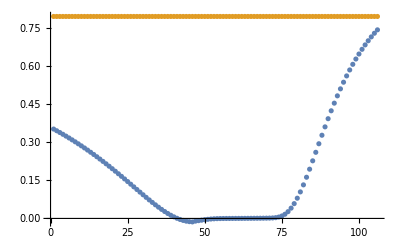

```mathematica
ListPlot[{DeleteCases[Lev4DoppTestsc[300,p/1000,1/1000,γ*10^6,0,0,6.2*Rbpress[300][[2]]*10^-6],Indeterminate],DeleteCases[Lev4DoppTestsc[300,0/1000,1/1000,γ*10^6,0,0,6.2*Rbpress[300][[2]]*10^-6],Indeterminate]}]
```

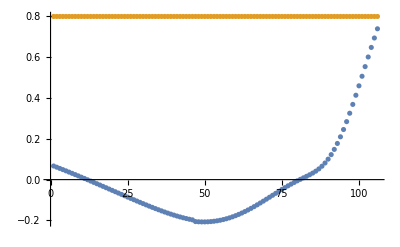

```mathematica
ListPlot[{DeleteCases[Lev4DoppTestsc[300,p/1000,1/1000,γ*10^6,0,0,2*Rbpress[300][[2]]*10^-6],Indeterminate],DeleteCases[Lev4DoppTestsc[300,0/1000,1/1000,γ*10^6,0,0,2*Rbpress[300][[2]]*10^-6],Indeterminate]}]
```

```mathematica
Tvw4D[400][[1]]
```

{0.,1.09848}

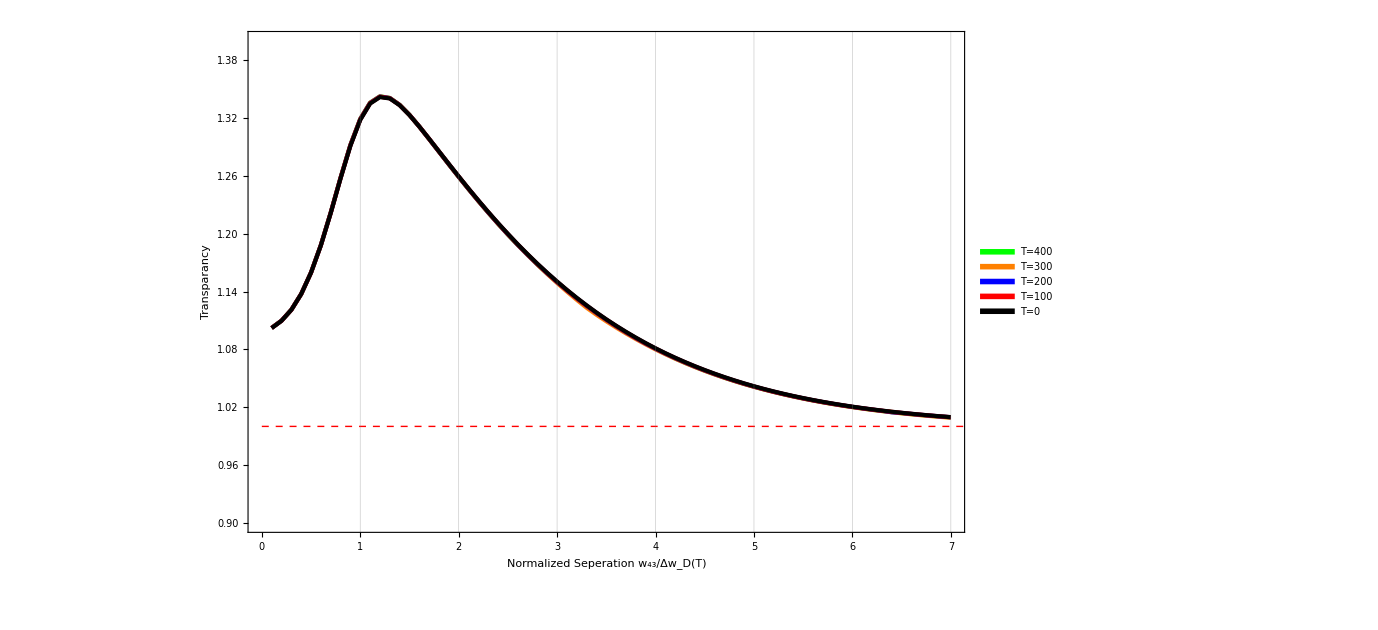

```mathematica
legend=
LineLegend[Thread[Directive[{Green,Orange,Blue,Red,Black,Pink,Purple,Gray},AbsoluteThickness[10]]],{Style["T=400",Green],Style["T=300",Orange],Style["T=200",Blue],Style["T=100",Red],Style["T=0",Black]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->20}];
MMMp0U=ListPlot[Table[Tvw4D[T],{T,{400,300,200,100,0}}],PlotLegends->Placed[legend,{Right,Center}],ImageSize->1020,Joined->True,
PlotStyle-> {{AbsoluteThickness[3],Green},{AbsoluteThickness[3],Orange},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black},{AbsoluteThickness[3],Pink},{AbsoluteThickness[3],Purple},{AbsoluteThickness[3],Gray}}
,PlotRange->{{0,7},{0.9,1.4}},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],GridLines->{{1,2,3,4,5,6,7,8},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]},Epilog->{Dashed,Red,Line[{{0,1},{7.90,1}}]}]
```

```mathematica
SetDirectory["C:\\Users\\Saesun Kim\\Desktop\\Saesun Kim\\Files\\EIT file\\Fig"]
Export["Figure9Combinedf1.eps",MMMp0]
Export["Figure9Combinedf1U.eps",MMMp0U]
```

C:\Users\Saesun Kim\Desktop\Saesun Kim\Files\EIT file\Fig

Figure9Combinedf1.eps

Figure9Combinedf1U.eps

γ=0.5 MHZ

```mathematica
Off[Power::infy];Off[Infinity::indet];
p=15.865;
γ=0.5;
Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1},
Do[
Print[T];
Tvw4γ5[T]={};Tvw3γ5[T]={};
Do[
list=Lev3DoppTestsc[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list1=Lev3DoppTestsc[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list3=Lev4DoppTestsc[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list4=Lev4DoppTestsc[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];

EIT=Min[DeleteCases[list,Indeterminate]];
EIT1=Min[DeleteCases[list3,Indeterminate]];

ABS=list1[[Position[list,EIT][[1]]]][[1]];
ABS1=list4[[Position[list3,EIT1][[1]]]][[1]];

Tvw4γ5[T]=Append[Tvw4γ5[T],{i,1-EIT1/ABS1}];
Tvw3γ5[T]=Append[Tvw3γ5[T],{i,1-EIT/ABS}];
,{i,0,7,0.1}]
,{T,{400,300,200,100,0,-100,-200,-250}}]
]
```

400

300

200

100

0

-100

-200

-250

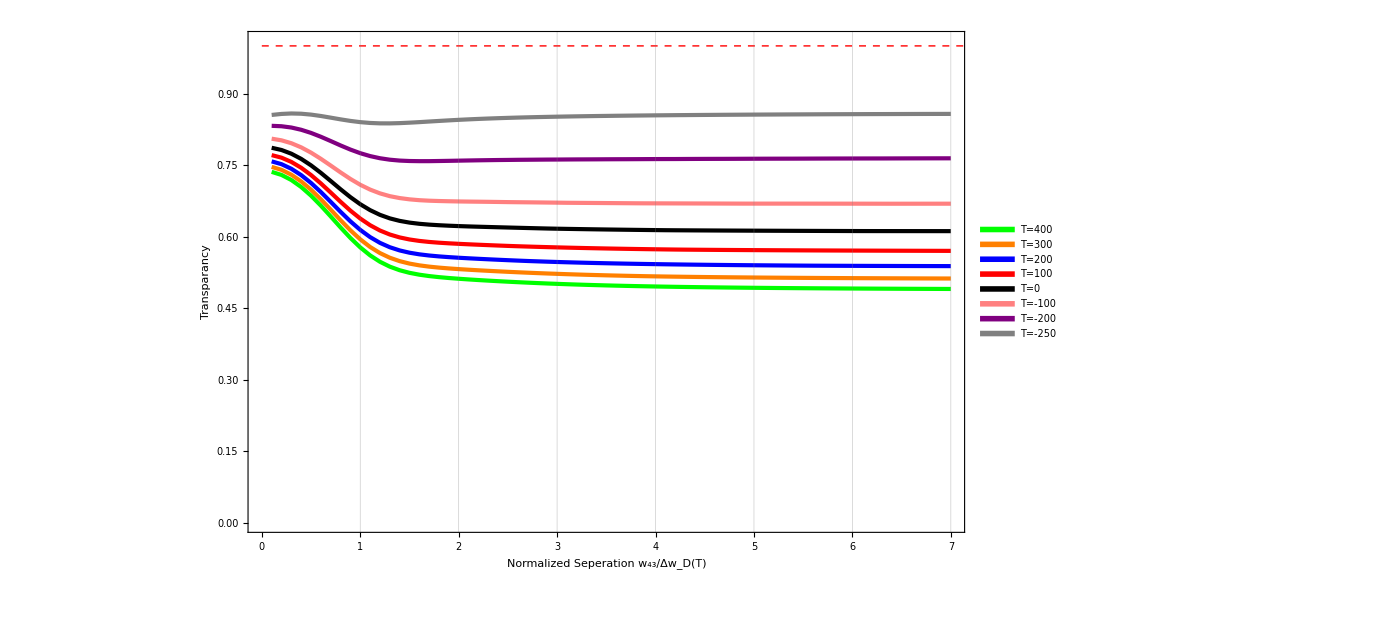

```mathematica
legend=
LineLegend[Thread[Directive[{Green,Orange,Blue,Red,Black,Pink,Purple,Gray},AbsoluteThickness[10]]],{Style["T=400",Green],Style["T=300",Orange],Style["T=200",Blue],Style["T=100",Red],Style["T=0",Black],Style["T=-100",Pink],Style["T=-200",Purple],Style["T=-250",Gray]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->20}];
MMM2=ListPlot[Table[Tvw4γ5[T],{T,{400,300,200,100,0,-100,-200,-250}}],PlotLegends->Placed[legend,{Right,Center}],ImageSize->1020,Joined->True,
PlotStyle-> {{AbsoluteThickness[3],Green},{AbsoluteThickness[3],Orange},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black},{AbsoluteThickness[3],Pink},{AbsoluteThickness[3],Purple},{AbsoluteThickness[3],Gray}}
,PlotRange->{{0,7},{0,1.01}},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],GridLines->{{1,2,3,4,5,6,7,8},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]},Epilog->{Dashed,Red,Line[{{0,1},{7.90,1}}]}]
```

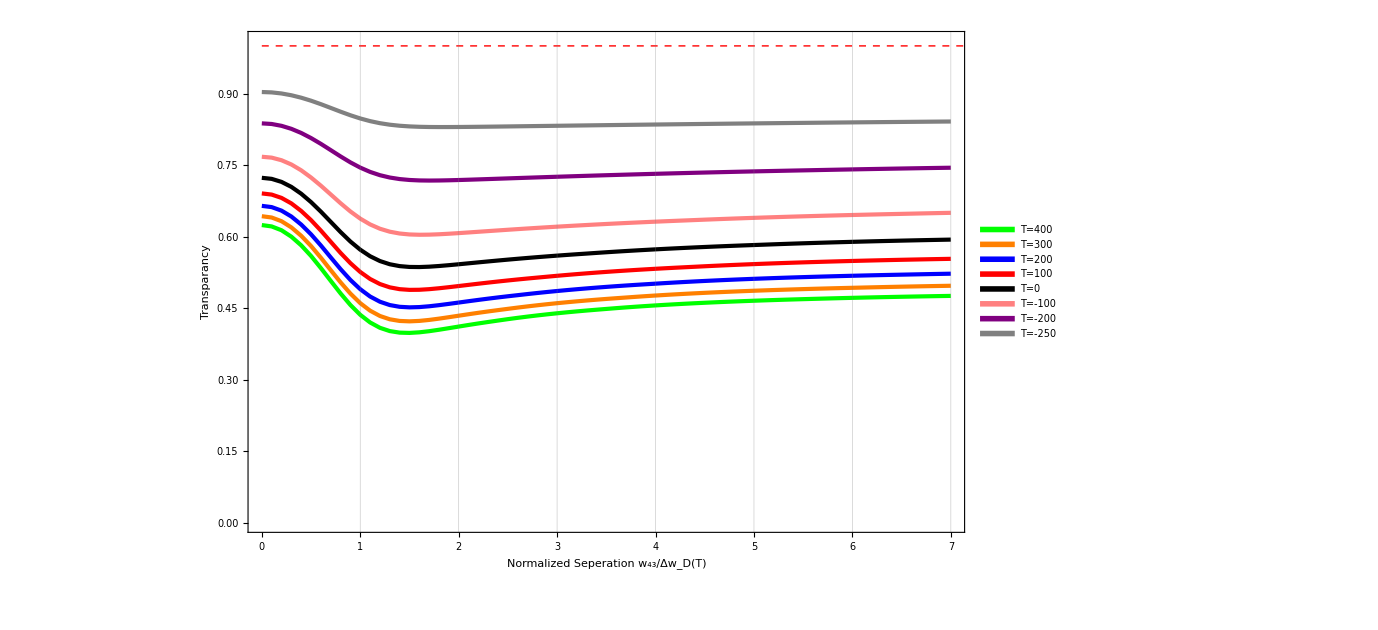

```mathematica
legend=
LineLegend[Thread[Directive[{Green,Orange,Blue,Red,Black,Pink,Purple,Gray},AbsoluteThickness[10]]],{Style["T=400",Green],Style["T=300",Orange],Style["T=200",Blue],Style["T=100",Red],Style["T=0",Black],Style["T=-100",Pink],Style["T=-200",Purple],Style["T=-250",Gray]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->20}];
MMM2=ListPlot[Table[Tvw3γ5[T],{T,{400,300,200,100,0,-100,-200,-250}}],PlotLegends->Placed[legend,{Right,Center}],ImageSize->1020,Joined->True,
PlotStyle-> {{AbsoluteThickness[3],Green},{AbsoluteThickness[3],Orange},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black},{AbsoluteThickness[3],Pink},{AbsoluteThickness[3],Purple},{AbsoluteThickness[3],Gray}}
,PlotRange->{{0,7},{0,1.01}},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],GridLines->{{1,2,3,4,5,6,7,8},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]},Epilog->{Dashed,Red,Line[{{0,1},{7.90,1}}]}]
```

γ=1.438MHZ

```mathematica
Off[Power::infy];Off[Infinity::indet];
p=15.865;
γ=1.438;
Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1},
Do[
Print[T];
Tvw4γ14[T]={};Tvw3γ14[T]={};
Do[
list=Lev3DoppTestsc[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list1=Lev3DoppTestsc[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list3=Lev4DoppTestsc[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list4=Lev4DoppTestsc[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];

EIT=Min[DeleteCases[list,Indeterminate]];
EIT1=Min[DeleteCases[list3,Indeterminate]];

ABS=list1[[Position[list,EIT][[1]]]][[1]];
ABS1=list4[[Position[list3,EIT1][[1]]]][[1]];

Tvw4γ14[T]=Append[Tvw4γ14[T],{i,1-EIT1/ABS1}];
Tvw3γ14[T]=Append[Tvw3γ14[T],{i,1-EIT/ABS}];
,{i,0,7,0.1}]
,{T,{400,300,200,100,0,-100,-200,-250}}]
]
```

400

300

200

100

0

-100

-200

-250

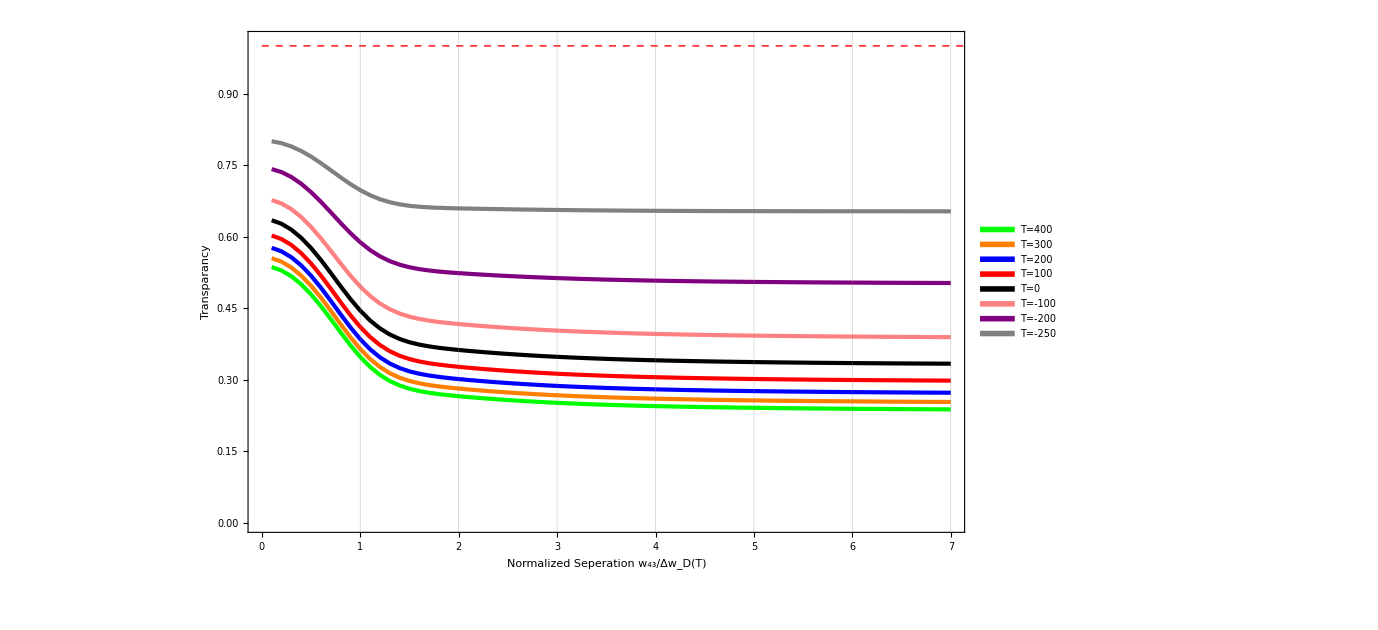

```mathematica
legend=
LineLegend[Thread[Directive[{Green,Orange,Blue,Red,Black,Pink,Purple,Gray},AbsoluteThickness[10]]],{Style["T=400",Green],Style["T=300",Orange],Style["T=200",Blue],Style["T=100",Red],Style["T=0",Black],Style["T=-100",Pink],Style["T=-200",Purple],Style["T=-250",Gray]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->20}];
MMM2=ListPlot[Table[Tvw4γ14[T],{T,{400,300,200,100,0,-100,-200,-250}}],PlotLegends->Placed[legend,{Right,Center}],ImageSize->1020,Joined->True,
PlotStyle-> {{AbsoluteThickness[3],Green},{AbsoluteThickness[3],Orange},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black},{AbsoluteThickness[3],Pink},{AbsoluteThickness[3],Purple},{AbsoluteThickness[3],Gray}}
,PlotRange->{{0,7},{0,1.01}},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],GridLines->{{1,2,3,4,5,6,7,8},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]},Epilog->{Dashed,Red,Line[{{0,1},{7.90,1}}]}]
```

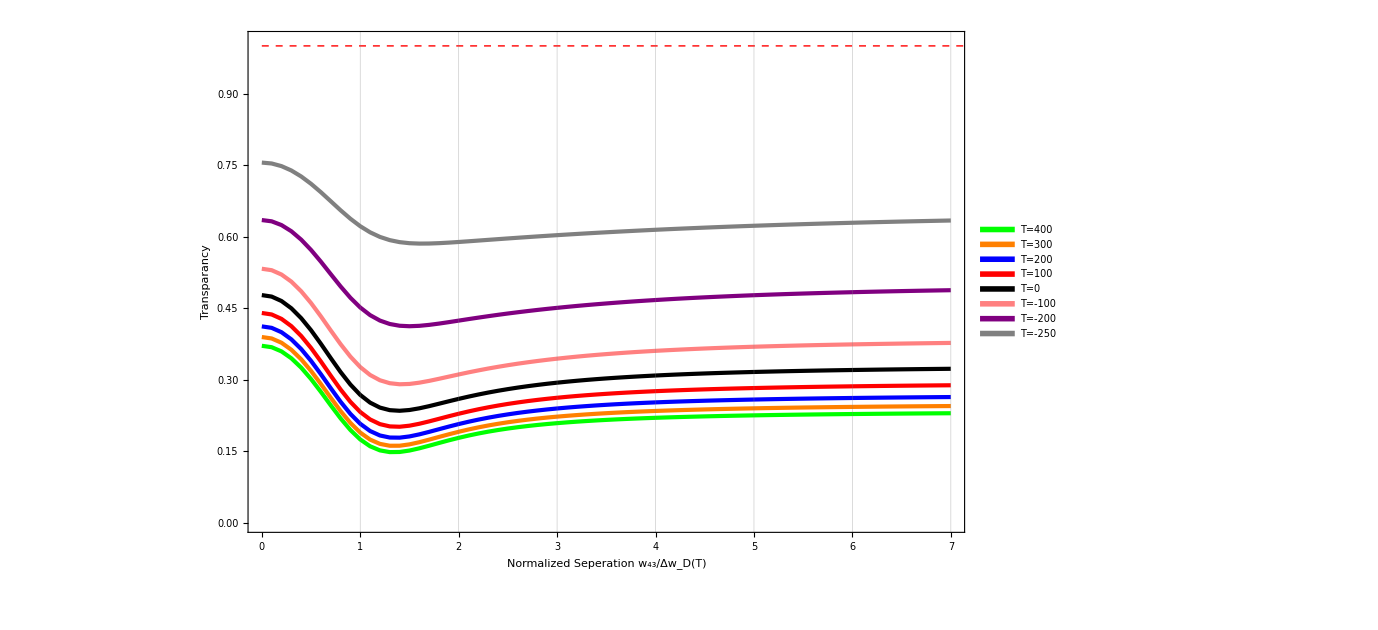

```mathematica
legend=
LineLegend[Thread[Directive[{Green,Orange,Blue,Red,Black,Pink,Purple,Gray},AbsoluteThickness[10]]],{Style["T=400",Green],Style["T=300",Orange],Style["T=200",Blue],Style["T=100",Red],Style["T=0",Black],Style["T=-100",Pink],Style["T=-200",Purple],Style["T=-250",Gray]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->20}];
MMM2=ListPlot[Table[Tvw3γ14[T],{T,{400,300,200,100,0,-100,-200,-250}}],PlotLegends->Placed[legend,{Right,Center}],ImageSize->1020,Joined->True,
PlotStyle-> {{AbsoluteThickness[3],Green},{AbsoluteThickness[3],Orange},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black},{AbsoluteThickness[3],Pink},{AbsoluteThickness[3],Purple},{AbsoluteThickness[3],Gray}}
,PlotRange->{{0,7},{0,1.01}},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],GridLines->{{1,2,3,4,5,6,7,8},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]},Epilog->{Dashed,Red,Line[{{0,1},{7.90,1}}]}]
```

## TvS vs Decoh

P=1

```mathematica
Off[Power::infy];Off[Infinity::indet];
p=1;
T=50;
Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1},
Do[
Print[γ];
Tvw41p1[γ]={};Tvw31p1[γ]={};
Do[
list=Lev3DoppTestsc[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list1=Lev3DoppTestsc[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list3=Lev4DoppTestsc[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list4=Lev4DoppTestsc[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];

EIT=Min[DeleteCases[list,Indeterminate]];
EIT1=Min[DeleteCases[list3,Indeterminate]];

ABS=list1[[Position[list,EIT][[1]]]][[1]];
ABS1=list4[[Position[list3,EIT1][[1]]]][[1]];

Tvw41p1[γ]=Append[Tvw41p1[γ],{i,1-EIT1/ABS1}];
Tvw31p1[γ]=Append[Tvw31p1[γ],{i,1-EIT/ABS}];
,{i,0,7,0.1}]
,{γ,{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1,1.1,1.2,1.3,1.4,1.5}}]
]
```

0

0.1

0.2

0.3

0.4

0.5

0.6

0.7

0.8

0.9

1

1.1

1.2

1.3

1.4

1.5

P=5

```mathematica
Off[Power::infy];Off[Infinity::indet];
p=5;
T=50;
Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1},
Do[
Print[γ];
Tvw41p5[γ]={};Tvw31p5[γ]={};
Do[
list=Lev3DoppTestsc[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list1=Lev3DoppTestsc[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list3=Lev4DoppTestsc[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list4=Lev4DoppTestsc[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];

EIT=Min[DeleteCases[list,Indeterminate]];
EIT1=Min[DeleteCases[list3,Indeterminate]];

ABS=list1[[Position[list,EIT][[1]]]][[1]];
ABS1=list4[[Position[list3,EIT1][[1]]]][[1]];

Tvw41p5[γ]=Append[Tvw41p5[γ],{i,1-EIT1/ABS1}];
Tvw31p5[γ]=Append[Tvw31p5[γ],{i,1-EIT/ABS}];
,{i,0,7,0.1}]
,{γ,{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1,1.1,1.2,1.3,1.4,1.5}}]
]
```

0

0.1

0.2

0.3

0.4

0.5

0.6

0.7

0.8

0.9

1

1.1

1.2

1.3

1.4

1.5

```mathematica
legend=
LineLegend[Thread[Directive[{Green,Orange,Blue,Red,Black,Pink,Purple,Gray,Darker[Green],Darker[Orange],Darker[Blue],Darker[Red],Darker[Gray],Darker[Pink],Darker[Purple],Darker[Yellow]},AbsoluteThickness[10]]],{Style["γ=0",Green],Style["0.1",Orange],Style["0.2",Blue],Style["0.3",Red],Style["0.4",Black],Style["0.5",Pink],Style["0.6",Purple],Style["0.7",Gray],Style["0.8",Darker[Green]],Style["0.9",Darker[Orange]],Style["1.0",Darker[Blue]],Style["1.1",Darker[Red]],Style["1.2",Darker[Gray]],Style["1.3",Darker[Pink]],Style["1.4",Darker[Purple]],Style["1.5",Darker[Yellow]]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->20}];
MMM2=ListPlot[Table[Tvw41p5[γ],{γ,{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1,1.1,1.2,1.3,1.4,1.5}}],PlotLegends->Placed[legend,{1.,Center}],ImageSize->1020,Joined->True,
PlotStyle-> {{AbsoluteThickness[3],Green},{AbsoluteThickness[3],Orange},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black},{AbsoluteThickness[3],Pink},{AbsoluteThickness[3],Purple},{AbsoluteThickness[3],Gray},{AbsoluteThickness[3],Darker[Green]},{AbsoluteThickness[3],Darker[Orange]},{AbsoluteThickness[3],Darker[Blue]},{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Darker[Gray]},{AbsoluteThickness[3],Darker[Pink]},{AbsoluteThickness[3],Darker[Purple]},{AbsoluteThickness[3],Darker[Yellow]}}
,PlotRange->{{0,7},All},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],GridLines->{{1,2,3,4,5,6,7,8},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]},Epilog->{Dashed,Red,Line[{{0,1},{7.90,1}}]}]
```

-Graphics-

```mathematica
legend=
LineLegend[Thread[Directive[{Green,Orange,Blue,Red,Black,Pink,Purple,Gray,Darker[Green],Darker[Orange],Darker[Blue],Darker[Red],Darker[Gray],Darker[Pink],Darker[Purple],Darker[Yellow]},AbsoluteThickness[10]]],{Style["γ=0",Green],Style["0.1",Orange],Style["0.2",Blue],Style["0.3",Red],Style["0.4",Black],Style["0.5",Pink],Style["0.6",Purple],Style["0.7",Gray],Style["0.8",Darker[Green]],Style["0.9",Darker[Orange]],Style["1.0",Darker[Blue]],Style["1.1",Darker[Red]],Style["1.2",Darker[Gray]],Style["1.3",Darker[Pink]],Style["1.4",Darker[Purple]],Style["1.5",Darker[Yellow]]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->20}];
MMM2=ListPlot[Table[Tvw31p5[γ],{γ,{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1,1.1,1.2,1.3,1.4,1.5}}],PlotLegends->Placed[legend,{1.,Center}],ImageSize->1020,Joined->True,
PlotStyle-> {{AbsoluteThickness[3],Green},{AbsoluteThickness[3],Orange},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black},{AbsoluteThickness[3],Pink},{AbsoluteThickness[3],Purple},{AbsoluteThickness[3],Gray},{AbsoluteThickness[3],Darker[Green]},{AbsoluteThickness[3],Darker[Orange]},{AbsoluteThickness[3],Darker[Blue]},{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Darker[Gray]},{AbsoluteThickness[3],Darker[Pink]},{AbsoluteThickness[3],Darker[Purple]},{AbsoluteThickness[3],Darker[Yellow]}}
,PlotRange->{{0,7},All},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],GridLines->{{1,2,3,4,5,6,7,8},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]},Epilog->{Dashed,Red,Line[{{0,1},{7.90,1}}]}]
```

-Graphics-

P=15.8

```mathematica
5.750056*0.25
5.750056*0.10
5.750056*0.05
5.750056*0.01
```

1.43751

0.575006

0.287503

0.0575006

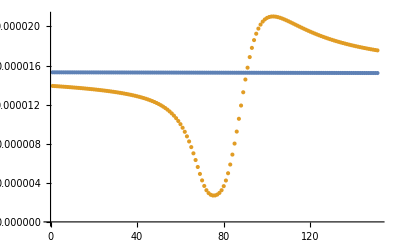

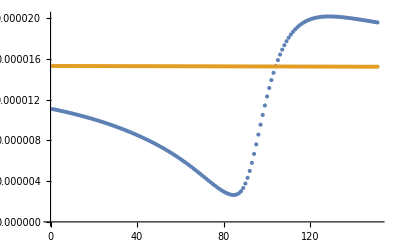

```mathematica
list=Lev3DoppTestscU[T,10/1000,1/1000,γ*10^6,0,0,1*Rbpress[T][[2]]*10^-6];
list1=Lev3DoppTestscU[T,0/1000,1/1000,γ*10^6,0,0,1*Rbpress[T][[2]]*10^-6];
list3=Lev4DoppTestscU[T,10/1000,1/1000,γ*10^6,0,0,1*Rbpress[T][[2]]*10^-6];
list4=Lev3DoppTestscU[T,0/1000,1/1000,γ*10^6,0,0,1*Rbpress[T][[2]]*10^-6];
ListPlot[{list1,list}]
ListPlot[{list3,list4},PlotRange->All]
```

```mathematica
Off[Power::infy];Off[Infinity::indet];
p=15.865;
T=50;
γ1=0;
Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1},
Do[
Print[γ];
Tvw41[γ]={};Tvw31[γ]={};
Do[
list=Lev3DoppTestsc[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list1=Lev3DoppTestsc[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list3=Lev4DoppTestsc[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list4=Lev3DoppTestsc[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];

EIT=Min[DeleteCases[list,Indeterminate]];
EIT1=Min[DeleteCases[list3,Indeterminate]];

ABS=list1[[Position[list,EIT][[1]]]][[1]];
ABS1=list4[[Position[list3,EIT1][[1]]]][[1]];
γ1=γ;
If[γ≠γ1,Print[{i,γ}]];
Tvw41[γ]=Append[Tvw41[γ],{i,1-EIT1/ABS1}];
Tvw31[γ]=Append[Tvw31[γ],{i,1-EIT/ABS}];
,{i,0.01,7,0.1}]
,{γ,{0,0.0575,0.287503,0.575006,1.43751,2.87502}}]
]
```

0

General::munfl: Exp[-711.826+0.395836 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-710.375-0.395432 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1111.1+0.494543 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Part::partw: Part {159} of {0.0000239775,0.000023977,0.0000239764,0.0000239759,0.0000239754,0.0000239748,0.0000239743,0.0000239738,0.0000239732,0.0000239727,0.0000239722,0.0000239716,0.0000239711,0.0000239706,0.00002397,0.0000239695,0.0000239689,0.0000239684,0.0000239679,«13»,0.0000239603,0.0000239597,0.0000239592,0.0000239586,0.0000239581,0.0000239575,0.000023957,0.0000239564,0.0000239559,0.0000239553,0.0000239548,0.0000239542,0.0000239537,0.0000239531,0.0000239526,0.000023952,0.0000239515,0.0000239509,«101»} does not exist.

Part::partw: Part {157} of {0.0000229565,0.0000229555,0.0000229545,0.0000229536,0.0000229526,0.0000229516,0.0000229506,0.0000229496,0.0000229486,0.0000229476,0.0000229466,0.0000229456,0.0000229446,0.0000229436,0.0000229426,0.0000229416,0.0000229407,0.0000229397,0.0000229387,«13»,0.0000229247,0.0000229237,0.0000229227,0.0000229217,0.0000229207,0.0000229196,0.0000229186,0.0000229176,0.0000229166,0.0000229156,0.0000229146,0.0000229136,0.0000229126,0.0000229116,0.0000229106,0.0000229096,0.0000229086,0.0000229076,«101»} does not exist.

0.0575

0.287503

0.575006

1.43751

2.87502

```mathematica
1.43751*2
```

2.87502

```mathematica
Tvw41[0]
```

{{0.01,1.09852},{0.11,1.10172},{0.21,1.10734},{0.31,1.11532},{0.41,1.12629},{0.51,1.14087},{0.61,1.15945},{0.71,1.18217},{0.81,1.20863},{0.91,1.23762}}

```mathematica
Tvw41[0]={{0.01,1.1},{0.11,1.1016393041390444},{0.21000000000000002,1.1071810605778631},{0.31000000000000005,1.1150951717008786},{0.41000000000000003,1.1260076511746406},{0.51,1.140512990273773},{0.6100000000000001,1.159031888945389},{0.7100000000000001,1.1816887027973415},{0.81,1.2080767338798286},{0.91,1.2370457768842082},{1.01,1.2664697850303444},{1.11,1.2936891941192106},{1.2100000000000002,1.3159839060407723},{1.31,1.3316404528881483},{1.4100000000000001,1.340264284379747},{1.51,1.342286143777197},{1.61,1.3390543604456528},{1.7100000000000002,1.3320207642088837},{1.81,1.3224167184032578},{1.9100000000000001,1.3111514668852808},{2.01,1.298841380098898},{2.11,1.2858855181658353},{2.21,1.2732896153304554},{2.31,1.2637041257275905},{2.41,1.2541736490853868},{2.51,1.2447442603447807},{2.61,1.2354473259760739},{2.71,1.2263059230120277},{2.81,1.2173381229358073},{2.91,1.208558631335558},{3.01,1.199979611474279},{3.11,1.191611121725626},{3.21,1.1834613771934852},{3.31,1.175536933006185},{3.41,1.1678428323076901},{3.51,1.1603827370915303},{3.61,1.1531590492121715},{3.71,1.1461730244132908},{3.81,1.139424880416004},{3.91,1.1329138994206263},{4.01,1.1266385251266287},{4.11,1.1205964542989375},{4.21,1.1147847228994798},{4.31,1.109199786819737},{4.41,1.1038375972763423},{4.51,1.0986936709604584},{4.61,1.0937631550594222},{4.71,1.0890408872943533},{4.8100000000000005,1.084521451139352},{4.91,1.0801992264062072},{5.01,1.07606843539318},{5.11,1.0721231848075534},{5.21,1.0683575036794521},{5.3100000000000005,1.0647653774892525},{5.41,1.0613407787330156},{5.51,1.0580776941501226},{5.61,1.0549701488349783},{5.71,1.0520122274505999},{5.8100000000000005,1.049198092756396},{5.91,1.0465220016557444},{6.01,1.043978318961325},{6.11,1.0415615290677935},{6.21,1.0392662457124708},{6.3100000000000005,1.037087977196371},{6.41,1.0350247062423843},{6.51,1.0330644989864153},{6.61,1.0312027801805397},{6.71,1.0294351250656244},{6.8100000000000005,1.0277625567474664},{6.91,1.0261791858384253}}
```

{{0.01,1.1},{0.11,1.10164},{0.21,1.10718},{0.31,1.1151},{0.41,1.12601},{0.51,1.14051},{0.61,1.15903},{0.71,1.18169},{0.81,1.20808},{0.91,1.23705},{1.01,1.26647},{1.11,1.29369},{1.21,1.31598},{1.31,1.33164},{1.41,1.34026},{1.51,1.34229},{1.61,1.33905},{1.71,1.33202},{1.81,1.32242},{1.91,1.31115},{2.01,1.29884},{2.11,1.28589},{2.21,1.27329},{2.31,1.2637},{2.41,1.25417},{2.51,1.24474},{2.61,1.23545},{2.71,1.22631},{2.81,1.21734},{2.91,1.20856},{3.01,1.19998},{3.11,1.19161},{3.21,1.18346},{3.31,1.17554},{3.41,1.16784},{3.51,1.16038},{3.61,1.15316},{3.71,1.14617},{3.81,1.13942},{3.91,1.13291},{4.01,1.12664},{4.11,1.1206},{4.21,1.11478},{4.31,1.1092},{4.41,1.10384},{4.51,1.09869},{4.61,1.09376},{4.71,1.08904},{4.81,1.08452},{4.91,1.0802},{5.01,1.07607},{5.11,1.07212},{5.21,1.06836},{5.31,1.06477},{5.41,1.06134},{5.51,1.05808},{5.61,1.05497},{5.71,1.05201},{5.81,1.0492},{5.91,1.04652},{6.01,1.04398},{6.11,1.04156},{6.21,1.03927},{6.31,1.03709},{6.41,1.03502},{6.51,1.03306},{6.61,1.0312},{6.71,1.02944},{6.81,1.02776},{6.91,1.02618}}

```mathematica
Off[Power::infy];Off[Infinity::indet];
p=15.865;
T=50;
γ1=0;
Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1},
Do[
Print[γ];
Tvw41[γ]={};Tvw31[γ]={};
Do[
list=Lev3DoppTestscU[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list1=Lev3DoppTestscU[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list3=Lev4DoppTestscU[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list4=Lev3DoppTestscU[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];

EIT=Min[DeleteCases[list,Indeterminate]];
EIT1=Min[DeleteCases[list3,Indeterminate]];

ABS=list1[[Position[list,EIT][[1]]]][[1]];
ABS1=list4[[Position[list3,EIT1][[1]]]][[1]];
γ1=γ;
If[γ≠γ1,Print[{i,γ}]];
Tvw41[γ]=Append[Tvw41[γ],{i,1-EIT1/ABS1}];
Tvw31[γ]=Append[Tvw31[γ],{i,1-EIT/ABS}];
,{i,0.01,7,0.1}]
,{γ,{0,0.0575,0.287503,0.575006,1.43751,2.87502}}]
]
```

0

General::munfl: Exp[-817.598+0.51957 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3268.53+1.03884 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3264.72-1.03824 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

0.0575

0.287503

0.575006

1.43751

2.87502

-Graphics-

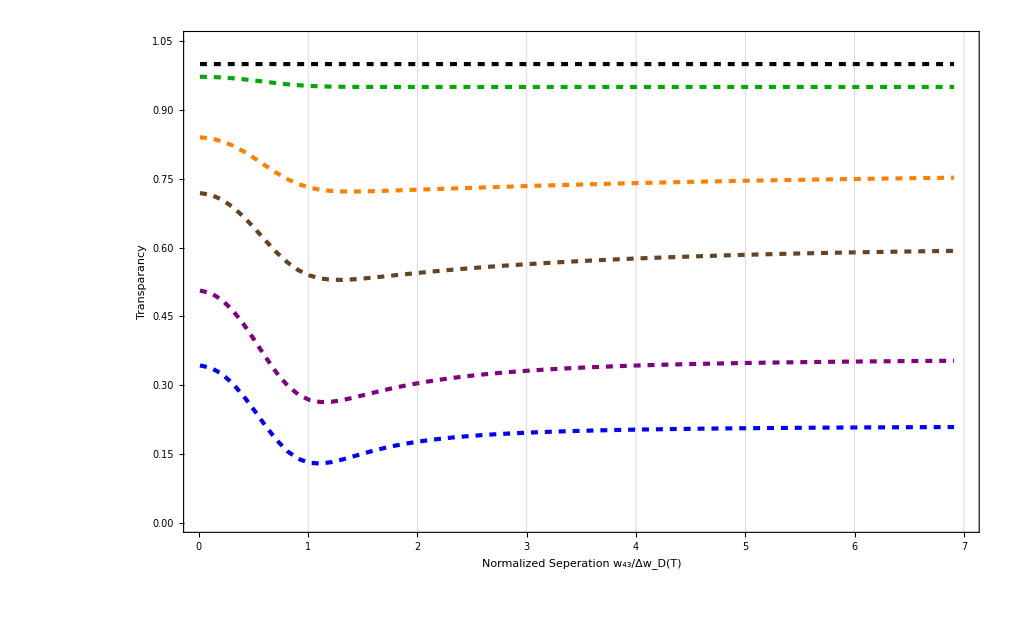

```mathematica
legend=
LineLegend[Thread[Directive[{Black,Darker[Green],Orange,Darker[Brown],Purple},AbsoluteThickness[10]]],{Style["γ=0",Black],Style["0.01γ",Darker[Green]],Style["0.05γ",Orange],Style["0.1γ",Darker[Brown]],Style["0.25γ",Purple]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->20}];
MMM1=ListPlot[Table[Tvw41U[γ],{γ,{0,0.0575,0.287503,0.575006,1.43751,2.87502}}],PlotLegends->Placed[legend,{1.,Center}],ImageSize->1020,Joined->True,
PlotStyle-> {{AbsoluteThickness[3],Black},{AbsoluteThickness[3],Darker[Green]},{AbsoluteThickness[3],Orange},{AbsoluteThickness[3],Darker[Brown]},{AbsoluteThickness[3],Purple},{AbsoluteThickness[3],Blue}}
,PlotRange->{{0,7},{0,1.5}},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],GridLines->{{1,2,3,4,5,6,7,8},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]}]
MMM2=ListPlot[Table[Tvw31U[γ],{γ,{0,0.0575,0.287503,0.575006,1.43751,2.87502}}],ImageSize->1020,Joined->True,
PlotStyle-> {{AbsoluteThickness[3],Black,Dashed},{AbsoluteThickness[3],Darker[Green],Dashed},{AbsoluteThickness[3],Orange,Dashed},{AbsoluteThickness[3],Darker[Brown],Dashed
},{AbsoluteThickness[3],Purple,Dashed},{AbsoluteThickness[3],Blue,Dashed}}
,PlotRange->{{0,7},{0,1.05}},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],GridLines->{{1,2,3,4,5,6,7,8},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]}]
```

```mathematica
MMMp15D=Show[MMM2,MMM1]
```

-Graphics-

```mathematica
Off[Power::infy];Off[Infinity::indet];
p=15.865;
T=50;
γ1=0;
Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1},
Do[
Print[γ];
Tvw41U[γ]={};Tvw31U[γ]={};
Do[
list=Lev3DoppTestsc[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list1=Lev3DoppTestsc[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list3=Lev4DoppTestsc[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list4=Lev3DoppTestsc[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];

EIT=Min[DeleteCases[list,Indeterminate]];
EIT1=Min[DeleteCases[list3,Indeterminate]];

ABS=list1[[Position[list,EIT][[1]]]][[1]];
ABS1=list4[[Position[list3,EIT1][[1]]]][[1]];
γ1=γ;
If[γ≠γ1,Print[{i,γ}]];
Tvw41U[γ]=Append[Tvw41U[γ],{i,1-EIT1/ABS1}];
Tvw31U[γ]=Append[Tvw31U[γ],{i,1-EIT/ABS}];
,{i,0.01,7,.1}]
,{γ,{0,0.0575,0.287503,0.575006,1.43751,2.87502}}]
]
```

0

General::munfl: Exp[-1067.74+0.593754 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1065.56-0.593148 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1666.64+0.741814 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

0.0575

0.287503

0.575006

1.43751

2.87502

```mathematica
Off[Power::infy];Off[Infinity::indet];
p=15.865;
T=50;
γ1=0;
Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1},
Do[
Print[γ];
Tvw41U[γ]={};Tvw31U[γ]={};
Do[
list=Lev3DoppTestsc[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list1=Lev3DoppTestsc[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list3=Lev4DoppTestsc[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list4=Lev3DoppTestsc[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];

EIT=Min[DeleteCases[list,Indeterminate]];
EIT1=Min[DeleteCases[list3,Indeterminate]];

ABS=list1[[Position[list,EIT][[1]]]][[1]];
ABS1=list4[[Position[list3,EIT1][[1]]]][[1]];
γ1=γ;
If[γ≠γ1,Print[{i,γ}]];
Tvw41U[γ]=Append[Tvw41U[γ],{i,1-EIT1/ABS1}];
Tvw31U[γ]=Append[Tvw31U[γ],{i,1-EIT/ABS}];
,{i,0.01,7,.1}]
,{γ,{0,0.0575,0.287503,0.575006,1.43751,2.87502}}]
]
```

```mathematica
Tvw41U[0]={{0.01,1.0985249295786805},{0.11,1.1026782099602206},{0.21000000000000002,1.1104583972020872},{0.31000000000000005,1.122187285446291},{0.41000000000000003,1.1390113312654115},{0.6100000000000001,1.190564579472672},{0.7100000000000001,1.2244790438491375},{0.81,1.2604819996904026},{0.91,1.2939270748285823},{1.01,1.3200733462312844},{1.11,1.336078138745411},{1.2100000000000002,1.3420289879221854},{1.31,1.3399635780088675},{1.4100000000000001,1.332605623192019},{1.51,1.3221340912619985},{1.61,1.3100332946714703},{1.7100000000000002,1.2971961324323842},{1.81,1.2841135960711527},{1.9100000000000001,1.2710446353056042},{2.01,1.2581583631428037},{2.11,1.24556991843278},{2.21,1.2332636262848211},{2.31,1.221310930867231},{2.41,1.2096042093824426},{2.51,1.1981789841290402},{2.61,1.1870654670129248},{2.71,1.176926272605261},{2.81,1.1673293467981745},{2.91,1.1580851865195423},{3.01,1.149199619180112},{3.11,1.140675751551611},{3.21,1.1325142618129613},{3.31,1.1247136764178167},{3.41,1.1172823077988554},{3.51,1.1103148847374489},{3.61,1.1036853607380235},{3.71,1.0973857722560358},{3.81,1.0914072724319364},{3.91,1.0857402996644314},{4.01,1.0803942971818432},{4.11,1.0753880725828098},{4.21,1.0706544841812875},{4.31,1.0661826552367566},{4.41,1.0619616614419416},{4.51,1.0579806062558639},{4.61,1.0542286857596683},{4.71,1.0506952439513644},{4.8100000000000005,1.0473698193606826},{4.91,1.0442421838244542},{5.01,1.0413023742178384},{5.11,1.038540717888836},{5.21,1.0359478524940067},{5.3100000000000005,1.0335147408832328},{5.41,1.0312326816315334},{5.51,1.0290933157670692},{5.61,1.027088630197081},{5.71,1.0252109582880098},{5.8100000000000005,1.0234529780127624},{5.91,1.0218077080371901},{6.01,1.020268502079514},{6.11,1.0188290418406731},{6.21,1.0174833287704461},{6.3100000000000005,1.01622567482227},{6.41,1.0150506990355297},{6.51,1.0137807776547623},{6.61,1.012960935764201},{6.71,1.0120041082894637},{6.8100000000000005,1.011111203261355},{6.91,1.0102781745570182}}
```

{{0.01,1.09852},{0.11,1.10268},{0.21,1.11046},{0.31,1.12219},{0.41,1.13901},{0.61,1.19056},{0.71,1.22448},{0.81,1.26048},{0.91,1.29393},{1.01,1.32007},{1.11,1.33608},{1.21,1.34203},{1.31,1.33996},{1.41,1.33261},{1.51,1.32213},{1.61,1.31003},{1.71,1.2972},{1.81,1.28411},{1.91,1.27104},{2.01,1.25816},{2.11,1.24557},{2.21,1.23326},{2.31,1.22131},{2.41,1.2096},{2.51,1.19818},{2.61,1.18707},{2.71,1.17693},{2.81,1.16733},{2.91,1.15809},{3.01,1.1492},{3.11,1.14068},{3.21,1.13251},{3.31,1.12471},{3.41,1.11728},{3.51,1.11031},{3.61,1.10369},{3.71,1.09739},{3.81,1.09141},{3.91,1.08574},{4.01,1.08039},{4.11,1.07539},{4.21,1.07065},{4.31,1.06618},{4.41,1.06196},{4.51,1.05798},{4.61,1.05423},{4.71,1.0507},{4.81,1.04737},{4.91,1.04424},{5.01,1.0413},{5.11,1.03854},{5.21,1.03595},{5.31,1.03351},{5.41,1.03123},{5.51,1.02909},{5.61,1.02709},{5.71,1.02521},{5.81,1.02345},{5.91,1.02181},{6.01,1.02027},{6.11,1.01883},{6.21,1.01748},{6.31,1.01623},{6.41,1.01505},{6.51,1.01378},{6.61,1.01296},{6.71,1.012},{6.81,1.01111},{6.91,1.01028}}

```mathematica
Lev4DoppTestsc[T_,P_,diam_,gam_,delt_,ab_,w_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Δ2,d31,d41},
d=Range[-0.002,0.002,0.0002]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d31=Sqrt[5/27]*2.537717 10^-29;
d41=Sqrt[4/27]*2.537717 10^-29;
d32=Sqrt[2/27]*2.537717 10^-29;
d42=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(w*10^6)  ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 



(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])


]
```

```mathematica
Off[Power::infy];Off[Infinity::indet];
p=15.865;
T=50;
γ1=0;
Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1},
Do[
Print[γ];
Tvw41U[γ]={};Tvw31U[γ]={};
Do[
list=Lev3DoppTestsc[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list1=Lev3DoppTestsc[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list3=Lev4DoppTestsc[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list4=Lev3DoppTestsc[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];

EIT=Min[list];
EIT1=Min[list3];

ABS=list1[[Position[list,EIT][[1]]]][[1]];
ABS1=list4[[Position[list3,EIT1][[1]]]][[1]];
γ1=γ;
If[γ≠γ1,Print[{i,γ}]];
Tvw41U[γ]=Append[Tvw41U[γ],{i,1-EIT1/ABS1}];
Tvw31U[γ]=Append[Tvw31U[γ],{i,1-EIT/ABS}];
,{i,0.01,7,.1}]
,{γ,{0.0575}}]
]
```

0.0575

General::munfl: Exp[-810.41] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-16339.8-3.31052 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-16170.9-2647. ⅈ] is too small to represent as a normalized machine number; precision may be lost.

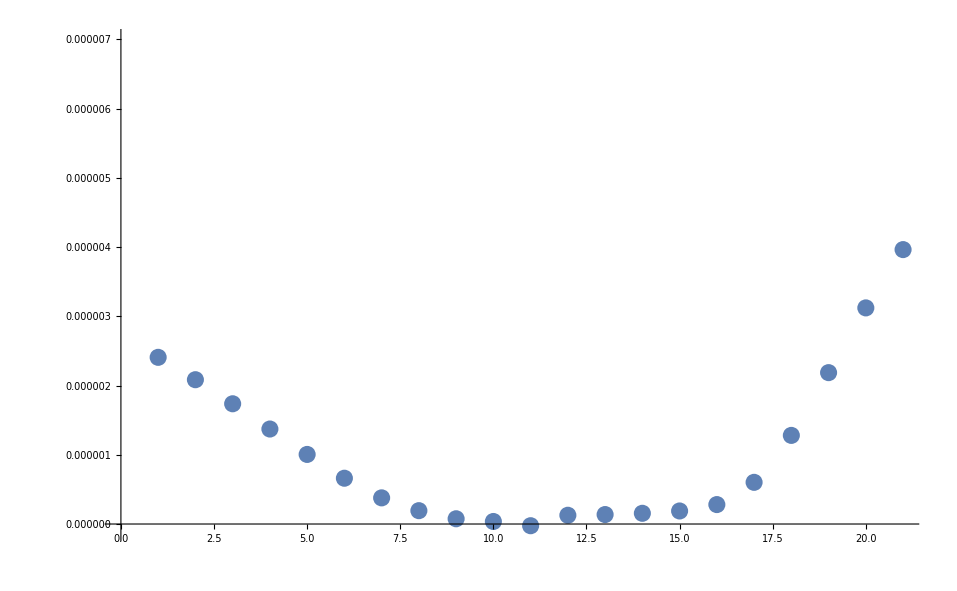

```mathematica
list3=Lev4DoppTestsc[T,p/1000,1/1000,0.0575*10^6,0,0,8*Rbpress[T][[2]]*10^-6];
list4=Lev4DoppTestsc[T,0/1000,1/1000,0.0575*10^6,0,0,0*Rbpress[T][[2]]*10^-6];
ListPlot[{list3,list4},PlotRange->{-1 10^-7,7*10^-6}]
```

```mathematica
Tvw41U[0.0575]
```

```mathematica
Tvw41U[0.0575]={{0.01,1.0985036694173846},{0.11,1.1009125093644445},{0.21000000000000002,1.1074561915233208},{0.31000000000000005,1.1186142278422224},{0.41000000000000003,1.1350743825318534},{0.51,1.1575157571487649},{0.6100000000000001,1.1861502100369123},{0.7100000000000001,1.2199961147928748},{0.81,1.256184529949123},{0.91,1.2900632908186784},{1.01,1.3167057675673908},{1.11,1.3330737092734797},{1.2100000000000002,1.339038425691549},{1.31,1.3365944898836168},{1.4100000000000001,1.3283633798490733},{1.51,1.317710417831616},{1.61,1.3055082503397637},{1.7100000000000002,1.2923230491007527},{1.81,1.2786600037358098},{1.9100000000000001,1.2648035691342057},{2.01,1.2509240640946002},{2.11,1.2380283051564178},{2.21,1.2257085953228117},{2.31,1.2136342086524627},{2.41,1.2018457600473291},{2.51,1.1903770429089353},{2.61,1.1792560605796196},{2.71,1.1685055967683344},{2.81,1.158143631366522},{2.91,1.1481837102972832},{3.01,1.1386353039718258},{3.11,1.12950416297037},{3.21,1.1207926710086886},{3.31,1.1125001926675646},{3.41,1.104623412784229},{3.51,1.0971566645140947},{3.61,1.0900922434290548},{3.71,1.0834207054671852},{3.81,1.0771311470219302},{3.91,1.0712114659232093},{4.01,1.0656486024997744},{4.11,1.060428760310539},{4.21,1.0555376064864772},{4.31,1.0509604519314137},{4.41,1.0466824118892162},{4.51,1.0426885475979593},{4.61,1.0389639899209664},{4.71,1.0354940459736395},{4.8100000000000005,1.0322642898573051},{4.91,1.0292606386710557},{5.01,1.0264694150037963},{5.11,1.0238773971154833},{5.21,1.02147185800279},{5.3100000000000005,1.0192405945137548},{5.41,1.017171947631836},{5.51,1.0152548149951899},{5.61,1.0134786566547507},{5.71,1.01183349500715},{5.8100000000000005,1.010309909767825},{5.91,1.00937909220623},{6.01,1.0087219235174136},{6.11,1.0081363955327673},{6.21,1.0076146153356238},{6.3100000000000005,1.0071494716434728},{6.41,1.0067345765873736},{6.61,1.0060332550766327},{6.71,1.0057371615850406},{6.8100000000000005,1.005471877719868},{6.91,1.0052338102469127}}
```

{{0.01,1.0985},{0.11,1.10091},{0.21,1.10746},{0.31,1.11861},{0.41,1.13507},{0.51,1.15752},{0.61,1.18615},{0.71,1.22},{0.81,1.25618},{0.91,1.29006},{1.01,1.31671},{1.11,1.33307},{1.21,1.33904},{1.31,1.33659},{1.41,1.32836},{1.51,1.31771},{1.61,1.30551},{1.71,1.29232},{1.81,1.27866},{1.91,1.2648},{2.01,1.25092},{2.11,1.23803},{2.21,1.22571},{2.31,1.21363},{2.41,1.20185},{2.51,1.19038},{2.61,1.17926},{2.71,1.16851},{2.81,1.15814},{2.91,1.14818},{3.01,1.13864},{3.11,1.1295},{3.21,1.12079},{3.31,1.1125},{3.41,1.10462},{3.51,1.09716},{3.61,1.09009},{3.71,1.08342},{3.81,1.07713},{3.91,1.07121},{4.01,1.06565},{4.11,1.06043},{4.21,1.05554},{4.31,1.05096},{4.41,1.04668},{4.51,1.04269},{4.61,1.03896},{4.71,1.03549},{4.81,1.03226},{4.91,1.02926},{5.01,1.02647},{5.11,1.02388},{5.21,1.02147},{5.31,1.01924},{5.41,1.01717},{5.51,1.01525},{5.61,1.01348},{5.71,1.01183},{5.81,1.01031},{5.91,1.00938},{6.01,1.00872},{6.11,1.00814},{6.21,1.00761},{6.31,1.00715},{6.41,1.00673},{6.61,1.00603},{6.71,1.00574},{6.81,1.00547},{6.91,1.00523}}

-Graphics-

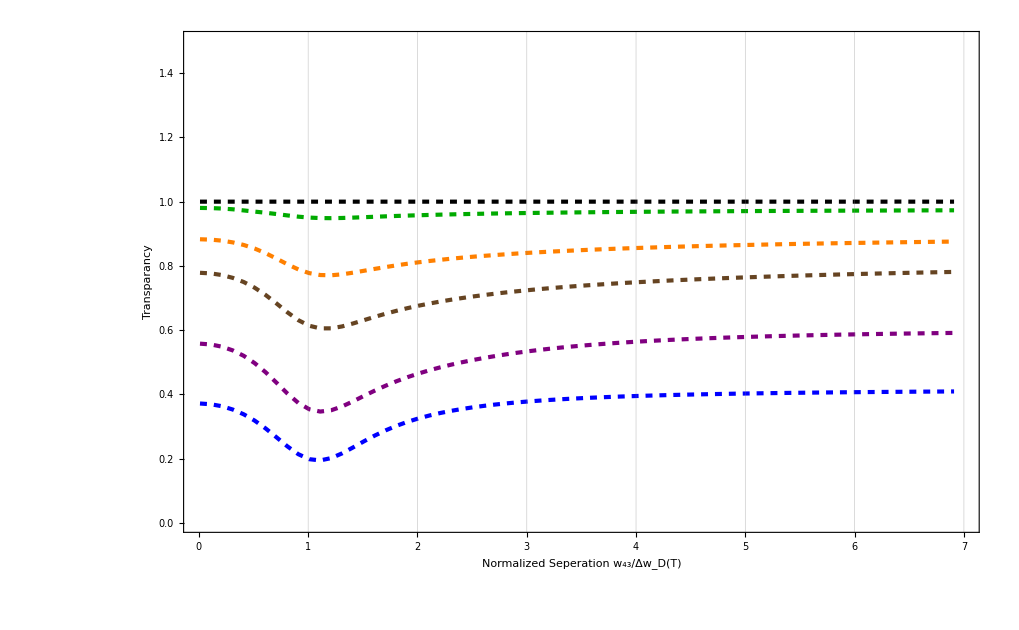

```mathematica
legend=
LineLegend[Thread[Directive[{Black,Darker[Green],Orange,Darker[Brown],Purple},AbsoluteThickness[10]]],{Style["γ=0",Black],Style["0.01γ",Darker[Green]],Style["0.05γ",Orange],Style["0.1γ",Darker[Brown]],Style["0.25γ",Purple]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->20}];
MMM1U=ListPlot[Table[Tvw41U[γ],{γ,{0,0.0575,0.287503,0.575006,1.43751,2.87502}}],PlotLegends->Placed[legend,{1.,Center}],ImageSize->1020,Joined->True,
PlotStyle-> {{AbsoluteThickness[3],Black},{AbsoluteThickness[3],Darker[Green]},{AbsoluteThickness[3],Orange},{AbsoluteThickness[3],Darker[Brown]},{AbsoluteThickness[3],Purple},{AbsoluteThickness[3],Blue}}
,PlotRange->{{0,7},{0,1.5}},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],GridLines->{{1,2,3,4,5,6,7,8},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]}]
MMM2U=ListPlot[Table[Tvw31U[γ],{γ,{0,0.0575,0.287503,0.575006,1.43751,2.87502}}],ImageSize->1020,Joined->True,
PlotStyle-> {{AbsoluteThickness[3],Black,Dashed},{AbsoluteThickness[3],Darker[Green],Dashed},{AbsoluteThickness[3],Orange,Dashed},{AbsoluteThickness[3],Darker[Brown],Dashed
},{AbsoluteThickness[3],Purple,Dashed},{AbsoluteThickness[3],Blue,Dashed}}
,PlotRange->{{0,7},{0,1.5}},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],GridLines->{{1,2,3,4,5,6,7,8},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]}]
```

```mathematica
MMMp15U=Show[MMM2U,MMM1U]
```

-Graphics-

```mathematica
SetDirectory["C:\\Users\\Saesun Kim\\Desktop\\Saesun Kim\\Files\\EIT file\\Fig"]
Export["Figure9Combinedf2.eps",MMMp15D]
Export["Figure9Combinedf2U.eps",MMMp15U]
```

C:\Users\Saesun Kim\Desktop\Saesun Kim\Files\EIT file\Fig

Figure9Combinedf2.eps

Figure9Combinedf2U.eps

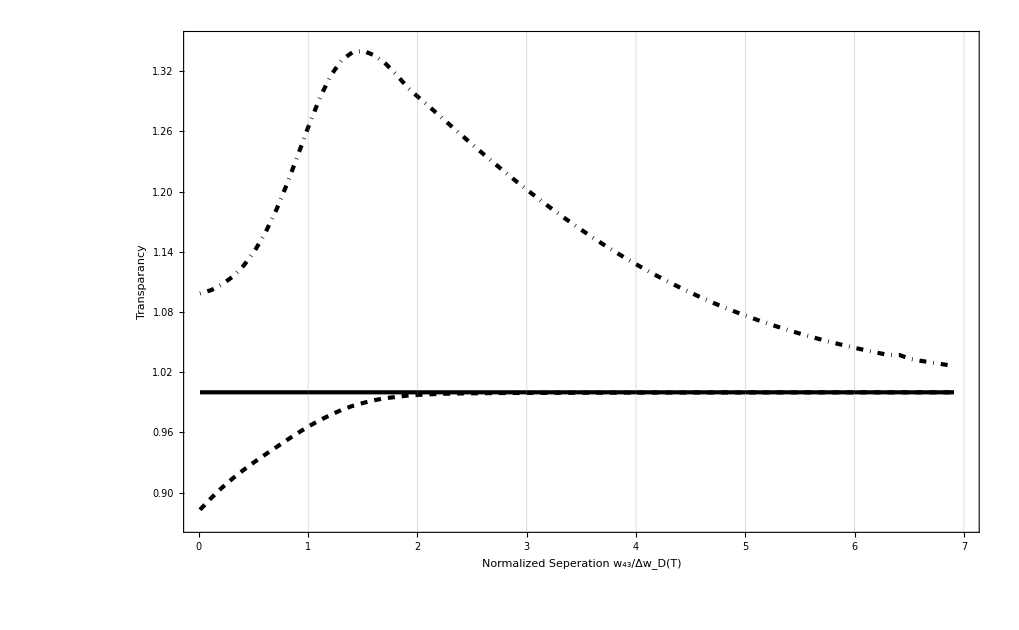

```mathematica
ListPlot[{Tvw31U[0],Tvw41U[0],Tvw41[0]},ImageSize->1020,Joined->True,
PlotStyle-> {{AbsoluteThickness[3],Black},{AbsoluteThickness[3],Black,Dashed},{AbsoluteThickness[3],Black,DotDashed}}
,PlotRange->{{0,7},{0.87,1.35}},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],GridLines->{{1,2,3,4,5,6,7,8},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]}]
```

```mathematica
Off[Power::infy];Off[Infinity::indet];
p=15.865;
T=50;
γ1=0;
Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1},
Do[
Print[γ];
Tvw41[γ]={};Tvw31[γ]={};
Do[
list=Lev3DoppTestsc[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list1=Lev3DoppTestsc[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list3=Lev4DoppTestsc[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list4=Lev3DoppTestsc[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];

EIT=Min[DeleteCases[list,Indeterminate]];
EIT1=Min[DeleteCases[list3,Indeterminate]];

ABS=list1[[Position[list,EIT][[1]]]][[1]];
ABS1=list4[[Position[list3,EIT1][[1]]]][[1]];
γ1=γ;
If[γ≠γ1,Print[{i,γ}]];
Tvw41[γ]=Append[Tvw41[γ],{i,1-EIT1/ABS1}];
Tvw31[γ]=Append[Tvw31[γ],{i,1-EIT/ABS}];
,{i,0.01,7,0.1}]
,{γ,{0,0.0575,0.287503,0.575006,1.43751,2.87502}}]
]
```

0

General::munfl: Exp[-711.826+0.395836 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-710.375-0.395432 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1111.1+0.494543 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

$Aborted

```mathematica
Lev3xsingleDoppTestscSep[T_,P_,diam_,gam_,delt_,k_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},
d=Range[-0.001,0.002,0.00001]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(0*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

{Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]],Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]],Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}[[k]]

]
```

```mathematica
Off[Power::infy];Off[Infinity::indet];
p=15.865;
T=50;
γ=2.87502;
Module[{list,list1,EIT,ABS},
Tvw31s[γ,1]={};Tvw31s[γ,2]={};Tvw31s[γ,3]={};
Do[
list=Lev3xsingleDoppTestscSep[T,p/1000,1/1000,γ*10^6,0,k];
list1=Lev3xsingleDoppTestscSep[T,0/1000,1/1000,γ*10^6,0,k];

EIT=Min[DeleteCases[list,Indeterminate]];

ABS=list1[[Position[list,EIT][[1]]]][[1]];

Tvw31s[γ,k]=Append[Tvw31s[γ,k],{i,1-EIT/ABS}];
,{i,0.01,7,0.1},{k,{1,2,3}}]

]
```

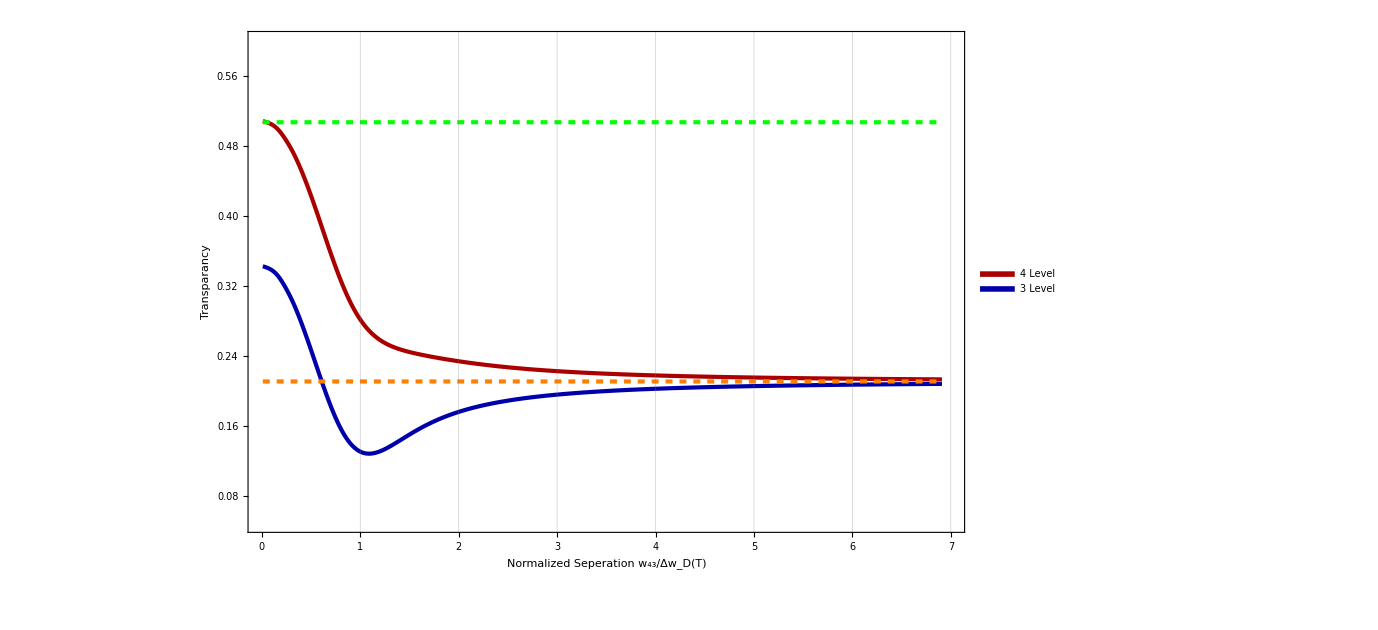

```mathematica
legend=
LineLegend[Thread[Directive[{Darker[Red],Darker[Blue]},AbsoluteThickness[10]]],{Style["4 Level",Darker[Red]],Style["3 Level",Darker[Blue]]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->50}];
MMMp15γ025=ListLinePlot[{Tvw41[2.87502],Tvw31[2.87502],Tvw31s[2.87502,1],Tvw31s[2.87502,2]},ImageSize->1020, InterpolationOrder->4,PlotLegends->Placed[legend,{0.8,0.7}],
PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Darker[Blue]},{AbsoluteThickness[3],Green,Dashed},{AbsoluteThickness[3],Orange,Dashed}}
,PlotRange->{{0,7},{0.05,0.6}},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],GridLines->{{1,2,3,4,5,6,7,8},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]}]
```

```mathematica
Lev3xsingleDoppTestscSepD[T_,P_,diam_,gam_,delt_,k_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},
d=Range[-0.001,0.002,0.00001]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d31=Sqrt[5/27]*2.537717 10^-29;
d41=Sqrt[4/27]*2.537717 10^-29;
d32=Sqrt[2/27]*2.537717 10^-29;
d42=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(0*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

{Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]],Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]],Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}[[k]]

]
```

```mathematica
Off[Power::infy];Off[Infinity::indet];
p=15.865;
T=50;
γ=2.87502;
Module[{list,list1,EIT,ABS},
Tvw31sD[γ,1]={};Tvw31sD[γ,2]={};Tvw31sD[γ,3]={};
Do[
list=Lev3xsingleDoppTestscSepD[T,p/1000,1/1000,γ*10^6,0,k];
list1=Lev3xsingleDoppTestscSepD[T,0/1000,1/1000,γ*10^6,0,k];

EIT=Min[DeleteCases[list,Indeterminate]];

ABS=list1[[Position[list,EIT][[1]]]][[1]];

Tvw31sD[γ,k]=Append[Tvw31sD[γ,k],{i,1-EIT/ABS}];
,{i,0.01,7,0.1},{k,{1,2,3}}]

]
```

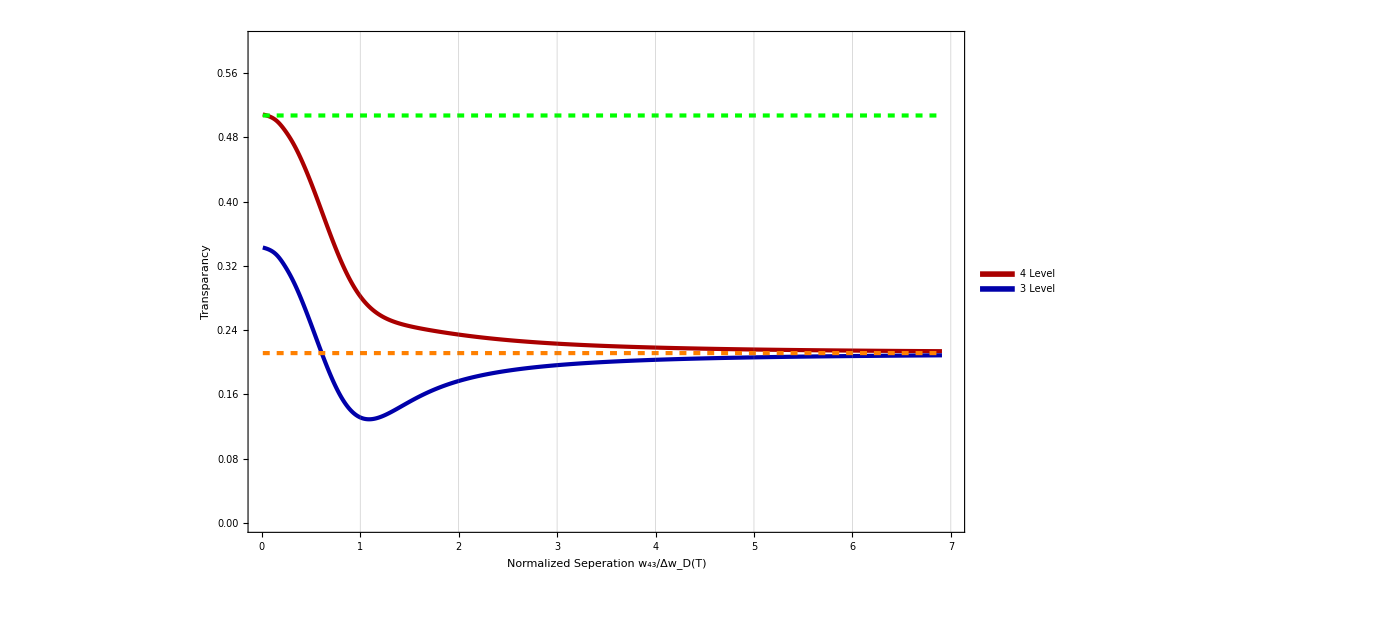

```mathematica
legend=
LineLegend[Thread[Directive[{Darker[Red],Darker[Blue]},AbsoluteThickness[10]]],{Style["4 Level",Darker[Red]],Style["3 Level",Darker[Blue]]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->50}];
MMMp15γ01D=ListLinePlot[{Tvw41[2.87502],Tvw31[2.87502],Tvw31s[2.87502,1],Tvw31s[2.87502,2]},ImageSize->1020, InterpolationOrder->4,PlotLegends->Placed[legend,{0.8,0.7}],
PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Darker[Blue]},{AbsoluteThickness[3],Green,Dashed},{AbsoluteThickness[3],Orange,Dashed}}
,PlotRange->{{0,7},{0,0.6}},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],GridLines->{{1,2,3,4,5,6,7,8},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]}]
```

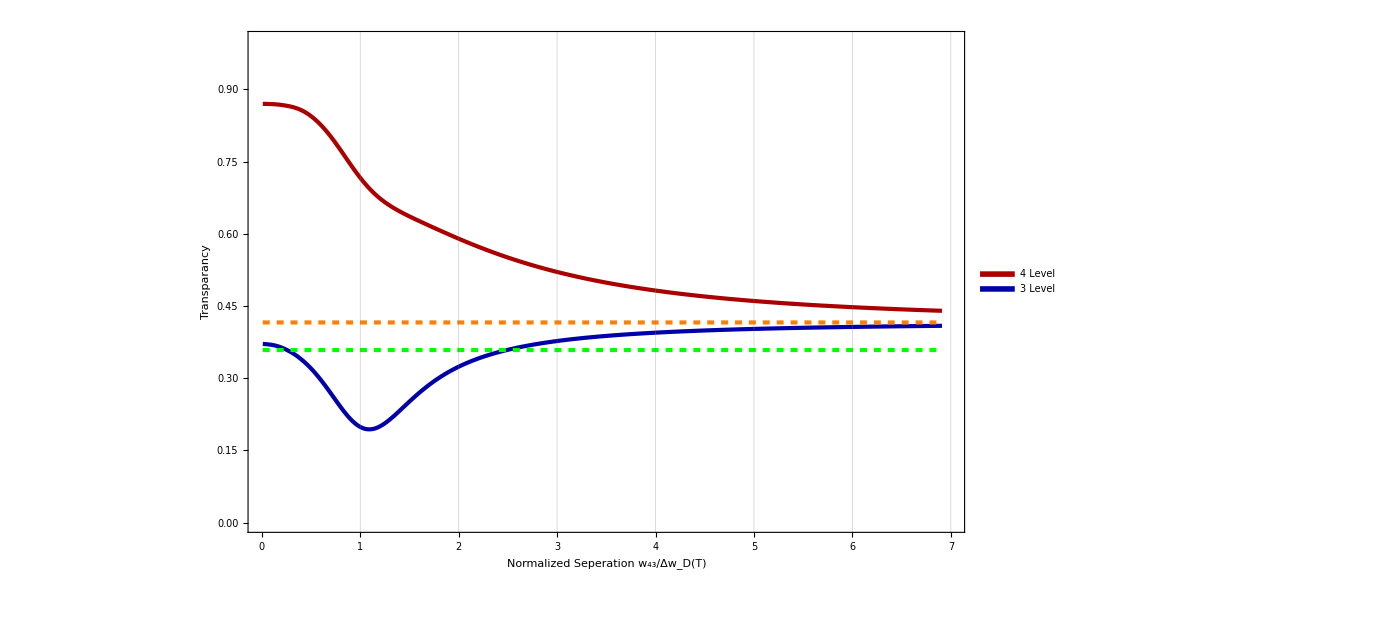

```mathematica
legend=
LineLegend[Thread[Directive[{Darker[Red],Darker[Blue]},AbsoluteThickness[10]]],{Style["4 Level",Darker[Red]],Style["3 Level",Darker[Blue]]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->50}];
MMMp15γ01=ListLinePlot[{Tvw41U[2.87502],Tvw31U[2.87502],Tvw31sD[2.87502,1],Tvw31sD[2.87502,2]},ImageSize->1020, InterpolationOrder->4,PlotLegends->Placed[legend,{0.8,0.7}],
PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Darker[Blue]},{AbsoluteThickness[3],Green,Dashed},{AbsoluteThickness[3],Orange,Dashed}}
,PlotRange->{{0,7},{0,1}},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],GridLines->{{1,2,3,4,5,6,7,8},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]}]
```

```mathematica
Off[Power::infy];Off[Infinity::indet];
p=15.865;
T=50;
γ=0.0575;
Module[{list,list1,EIT,ABS},
Tvw31sD[γ,1]={};Tvw31sD[γ,2]={};Tvw31sD[γ,3]={};
Do[
list=Lev3xsingleDoppTestscSepD[T,p/1000,1/1000,γ*10^6,0,k];
list1=Lev3xsingleDoppTestscSepD[T,0/1000,1/1000,γ*10^6,0,k];

EIT=Min[DeleteCases[list,Indeterminate]];

ABS=list1[[Position[list,EIT][[1]]]][[1]];

Tvw31sD[γ,k]=Append[Tvw31sD[γ,k],{i,1-EIT/ABS}];
,{i,0.01,7,0.1},{k,{1,2,3}}]

]
```

General::munfl: Exp[-740.735-264.566 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-810.41] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-740.735+264.566 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
Off[Power::infy];Off[Infinity::indet];
p=15.865;
T=50;
γ=0.0575;
Module[{list,list1,EIT,ABS},
Tvw31s[γ,1]={};Tvw31s[γ,2]={};Tvw31s[γ,3]={};
Do[
list=Select[Lev3xsingleDoppTestscSep[T,p/1000,1/1000,γ*10^6,0,k],#≠0&];
list1=Lev3xsingleDoppTestscSep[T,0/1000,1/1000,γ*10^6,0,k];

EIT=Min[DeleteCases[list,Indeterminate]];

ABS=list1[[Position[list,EIT][[1]]]][[1]];

Tvw31s[γ,k]=Append[Tvw31s[γ,k],{i,1-EIT/ABS}];
,{i,0.01,7,0.1},{k,{1,2,3}}]

]
```

General::munfl: Exp[-714.974-1019.95 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1110.09-875.699 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1448.7-518.335 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

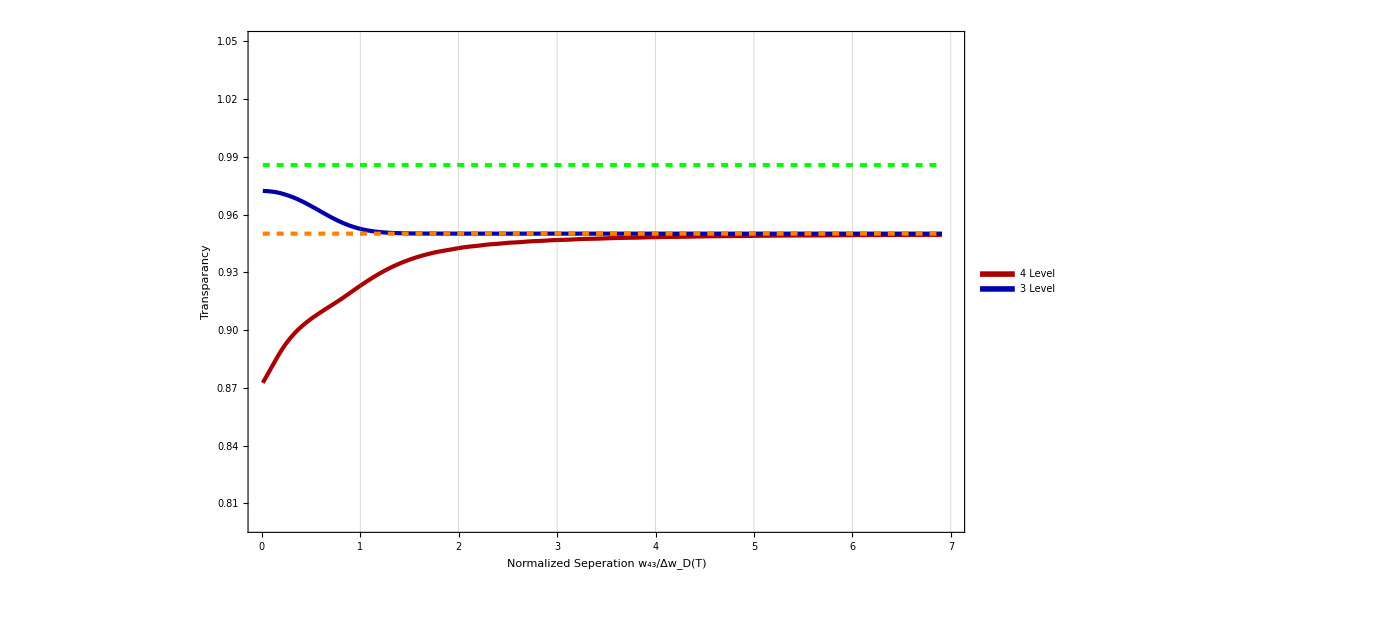

```mathematica
legend=
LineLegend[Thread[Directive[{Darker[Red],Darker[Blue]},AbsoluteThickness[10]]],{Style["4 Level",Darker[Red]],Style["3 Level",Darker[Blue]]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->50}];
MMMp15γ025D2=ListLinePlot[{Tvw41[0.0575],Tvw31[0.0575],Tvw31s[0.0575,1],Tvw31s[0.0575,2]},ImageSize->1020, InterpolationOrder->4,PlotLegends->Placed[legend,{0.8,0.7}],
PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Darker[Blue]},{AbsoluteThickness[3],Green,Dashed},{AbsoluteThickness[3],Orange,Dashed}}
,PlotRange->{{0,7},{0.8,1.05}},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],GridLines->{{1,2,3,4,5,6,7,8},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]}]
```

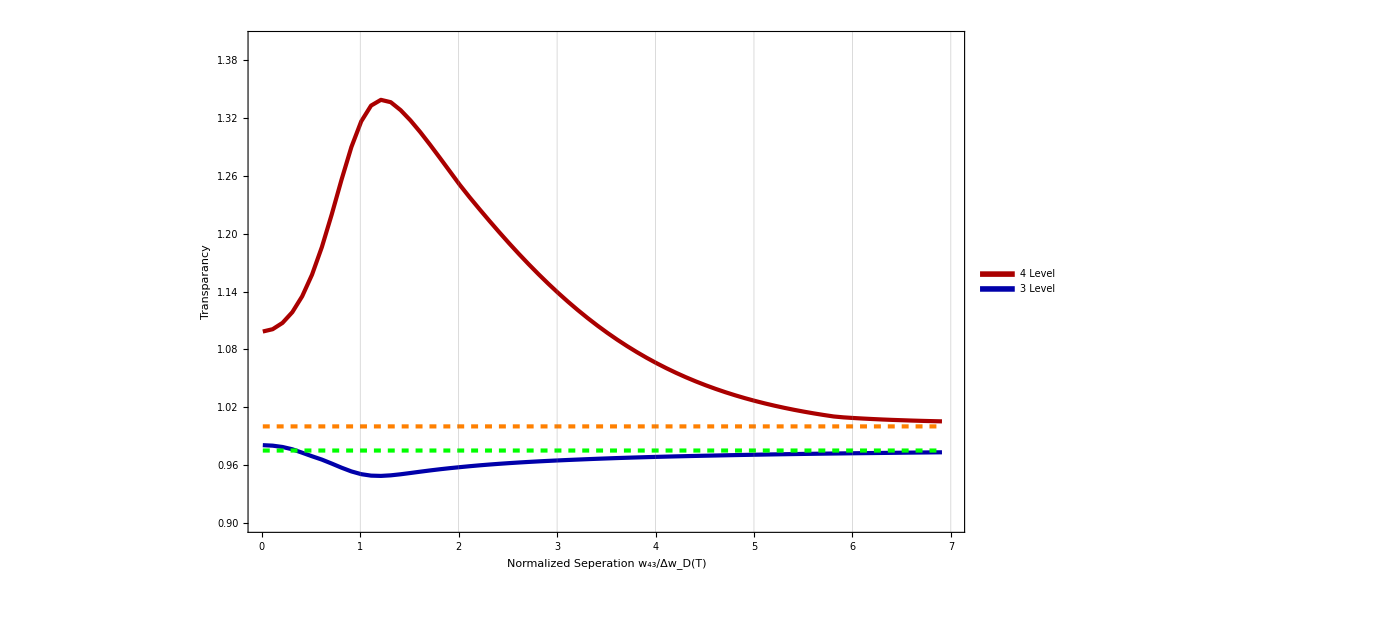

```mathematica
legend=
LineLegend[Thread[Directive[{Darker[Red],Darker[Blue]},AbsoluteThickness[10]]],{Style["4 Level",Darker[Red]],Style["3 Level",Darker[Blue]]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->50}];
MMMp15γ0051=ListLinePlot[{Tvw41U[0.0575],Tvw31U[0.0575],Tvw31sD[0.0575,1],Tvw31sD[0.0575,2]},ImageSize->1020, InterpolationOrder->1,PlotLegends->Placed[legend,{0.8,0.81}],
PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Darker[Blue]},{AbsoluteThickness[3],Green,Dashed},{AbsoluteThickness[3],Orange,Dashed}}
,PlotRange->{{0,7},{0.90,1.4}},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],GridLines->{{1,2,3,4,5,6,7,8},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]}]
```

```mathematica
SetDirectory["C:\\Users\\Saesun Kim\\Desktop\\Saesun Kim\\Files\\EIT file\\Fig"]
Export["Figure9g1.eps",MMMp15γ01D]
Export["Figure9g2.eps",MMMp15γ01]
Export["Figure9g3.eps",MMMp15γ025D2]
Export["Figure9g4.eps",MMMp15γ0051]
```

C:\Users\Saesun Kim\Desktop\Saesun Kim\Files\EIT file\Fig

Figure9g1.eps

Figure9g2.eps

Figure9g3.eps

Figure9g4.eps

```mathematica
Off[Power::infy];Off[Infinity::indet];
p=15.865;
T=50;
γ=0.0575;
Module[{list,list1,EIT,ABS},
Tvw31sD[γ,1]={};Tvw31sD[γ,2]={};Tvw31sD[γ,3]={};
Do[
list=Lev3xsingleDoppTestscSepD[T,p/1000,1/1000,γ*10^6,0,k];
list1=Lev3xsingleDoppTestscSepD[T,0/1000,1/1000,γ*10^6,0,k];

EIT=Min[DeleteCases[list,Indeterminate]];

ABS=list1[[Position[list,EIT][[1]]]][[1]];

Tvw31sD[γ,k]=Append[Tvw31sD[γ,k],{i,1-EIT/ABS}];
,{i,0.01,7,0.1},{k,{1,2,3}}]

]
```

$Aborted

```mathematica
legend=
LineLegend[Thread[Directive[{Darker[Red],Darker[Blue]},AbsoluteThickness[10]]],{Style["4 Level",Darker[Red]],Style["3 Level",Darker[Blue]]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->50}];
MMMp15γ005D=ListLinePlot[{Tvw41[0.0575],Tvw31[0.0575],Tvw31sD[0.0575,1],Tvw31sD[0.0575,2],Tvw31sD[0.0575,3]},ImageSize->1020, InterpolationOrder->1,PlotLegends->Placed[legend,{0.8,0.81}],
PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Darker[Blue]},{AbsoluteThickness[3],Green,Dashed},{AbsoluteThickness[3],Orange,Dashed},{AbsoluteThickness[3],Black,Dashed}}
,PlotRange->{{0,7},{0.85,1.05}},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],GridLines->{{1,2,3,4,5,6,7,8},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]}]
```

```mathematica
SetDirectory["D:\\Qsync\\PersonalFolders\\Saesun\\Papers\\Paper\\Final-Paper Figure"]
Export["Figure9Combinedf4.eps",MMMp15γ005]
```

D:\Qsync\PersonalFolders\Saesun\Papers\Paper\Final-Paper Figure

Figure9Combinedf4.eps

P=50

```mathematica
Off[Power::infy];Off[Infinity::indet];
p=50;
T=50;
Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1},
Do[
Print[γ];
Tvw41p50[γ]={};Tvw31p50[γ]={};
Do[
list=Lev3DoppTestsc[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list1=Lev3DoppTestsc[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list3=Lev4DoppTestsc[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list4=Lev4DoppTestsc[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];

EIT=Min[DeleteCases[list,Indeterminate]];
EIT1=Min[DeleteCases[list3,Indeterminate]];

ABS=list1[[Position[list,EIT][[1]]]][[1]];
ABS1=list4[[Position[list3,EIT1][[1]]]][[1]];

Tvw41p50[γ]=Append[Tvw41p50[γ],{i,1-EIT1/ABS1}];
Tvw31p50[γ]=Append[Tvw31p50[γ],{i,1-EIT/ABS}];
,{i,0,7,0.1}]
,{γ,{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1,1.1,1.2,1.3,1.4,1.5}}]
]
```

0

0.1

0.2

0.3

0.4

0.5

0.6

0.7

0.8

0.9

1

1.1

1.2

1.3

1.4

1.5

```mathematica
legend=
LineLegend[Thread[Directive[{Green,Orange,Blue,Red,Black,Pink,Purple,Gray,Darker[Green],Darker[Orange],Darker[Blue],Darker[Red],Darker[Gray],Darker[Pink],Darker[Purple],Darker[Yellow]},AbsoluteThickness[10]]],{Style["γ=0",Green],Style["0.1",Orange],Style["0.2",Blue],Style["0.3",Red],Style["0.4",Black],Style["0.5",Pink],Style["0.6",Purple],Style["0.7",Gray],Style["0.8",Darker[Green]],Style["0.9",Darker[Orange]],Style["1.0",Darker[Blue]],Style["1.1",Darker[Red]],Style["1.2",Darker[Gray]],Style["1.3",Darker[Pink]],Style["1.4",Darker[Purple]],Style["1.5",Darker[Yellow]]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->20}];
MMM2=ListPlot[Table[Tvw41p50[γ],{γ,{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1,1.1,1.2,1.3,1.4,1.5}}],PlotLegends->Placed[legend,{1.,Center}],ImageSize->1020,Joined->True,
PlotStyle-> {{AbsoluteThickness[3],Green},{AbsoluteThickness[3],Orange},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black},{AbsoluteThickness[3],Pink},{AbsoluteThickness[3],Purple},{AbsoluteThickness[3],Gray},{AbsoluteThickness[3],Darker[Green]},{AbsoluteThickness[3],Darker[Orange]},{AbsoluteThickness[3],Darker[Blue]},{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Darker[Gray]},{AbsoluteThickness[3],Darker[Pink]},{AbsoluteThickness[3],Darker[Purple]},{AbsoluteThickness[3],Darker[Yellow]}}
,PlotRange->{{0,7},All},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],GridLines->{{1,2,3,4,5,6,7,8},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]},Epilog->{Dashed,Red,Line[{{0,1},{7.90,1}}]}]
```

-Graphics-

```mathematica
legend=
LineLegend[Thread[Directive[{Green,Orange,Blue,Red,Black,Pink,Purple,Gray,Darker[Green],Darker[Orange],Darker[Blue],Darker[Red],Darker[Gray],Darker[Pink],Darker[Purple],Darker[Yellow]},AbsoluteThickness[10]]],{Style["γ=0",Green],Style["0.1",Orange],Style["0.2",Blue],Style["0.3",Red],Style["0.4",Black],Style["0.5",Pink],Style["0.6",Purple],Style["0.7",Gray],Style["0.8",Darker[Green]],Style["0.9",Darker[Orange]],Style["1.0",Darker[Blue]],Style["1.1",Darker[Red]],Style["1.2",Darker[Gray]],Style["1.3",Darker[Pink]],Style["1.4",Darker[Purple]],Style["1.5",Darker[Yellow]]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->20}];
MMM2=ListPlot[Table[Tvw31p50[γ],{γ,{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1,1.1,1.2,1.3,1.4,1.5}}],PlotLegends->Placed[legend,{1.,Center}],ImageSize->1020,Joined->True,
PlotStyle-> {{AbsoluteThickness[3],Green},{AbsoluteThickness[3],Orange},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black},{AbsoluteThickness[3],Pink},{AbsoluteThickness[3],Purple},{AbsoluteThickness[3],Gray},{AbsoluteThickness[3],Darker[Green]},{AbsoluteThickness[3],Darker[Orange]},{AbsoluteThickness[3],Darker[Blue]},{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Darker[Gray]},{AbsoluteThickness[3],Darker[Pink]},{AbsoluteThickness[3],Darker[Purple]},{AbsoluteThickness[3],Darker[Yellow]}}
,PlotRange->{{0,7},All},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],GridLines->{{1,2,3,4,5,6,7,8},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]},Epilog->{Dashed,Red,Line[{{0,1},{7.90,1}}]}]
```

-Graphics-

P=100

```mathematica
Off[Power::infy];Off[Infinity::indet];
p=100;
T=50;
Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1},
Do[
Print[γ];
Tvw41[γ]={};Tvw31[γ]={};
Do[
list=Lev3DoppTestsc[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list1=Lev3DoppTestsc[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list3=Lev4DoppTestsc[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list4=Lev4DoppTestsc[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];

EIT=Min[DeleteCases[list,Indeterminate]];
EIT1=Min[DeleteCases[list3,Indeterminate]];

ABS=list1[[Position[list,EIT][[1]]]][[1]];
ABS1=list4[[Position[list3,EIT1][[1]]]][[1]];

Tvw41[γ]=Append[Tvw41[γ],{i,1-EIT1/ABS1}];
Tvw31[γ]=Append[Tvw31[γ],{i,1-EIT/ABS}];
,{i,0,7,0.05}]
,{γ,{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1,1.1,1.2,1.3,1.4,1.5}}]
]
```

0

0.1

0.2

0.3

0.4

0.5

$Aborted

```mathematica
Effect of two close excited state
```

## TvS vs Power

γ=0

```mathematica
Off[Power::infy];Off[Infinity::indet];Off[General::ovfl];
γ=0;
T=50;
Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1},
Do[
Print[p];
Tvw42γ0[p]={};Tvw32γ0[p]={};
Do[
list=Lev3DoppTestscp[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list1=Lev3DoppTestscp[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list3=Lev4DoppTestscp[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list4=Lev4DoppTestscp[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];

EIT=Min[DeleteCases[list,Indeterminate]];
EIT1=Min[DeleteCases[list3,Indeterminate]];

ABS=list1[[Position[list,EIT][[1]]]][[1]];
ABS1=list4[[Position[list3,EIT1][[1]]]][[1]];

Tvw42γ0[p]=Append[Tvw42γ0[p],{i,1-EIT1/ABS1}];
Tvw32γ0[p]=Append[Tvw32γ0[p],{i,1-EIT/ABS}];
,{i,0,5,0.25}]
,{p,{0,5,10,15,20}}]
]
```

0

5

10

15

20

```mathematica
legend=
LineLegend[Thread[Directive[{Green,Orange,Blue,Red,Black,Pink,Purple,Gray},AbsoluteThickness[10]]],{Style["P=0",Green],Style["5",Orange],Style["10",Blue],Style["15",Red],Style["20",Red]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->20}];
MMM2=ListPlot[Table[Tvw42γ0[p],{p,{0,5,10,15,20}}],PlotLegends->Placed[legend,{1.,Center}],ImageSize->1020,Joined->True,
PlotStyle-> {{AbsoluteThickness[3],Green},{AbsoluteThickness[3],Orange},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black},{AbsoluteThickness[3],Pink},{AbsoluteThickness[3],Purple},{AbsoluteThickness[3],Gray}}
,PlotRange->{{0,7},All},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],GridLines->{{1,2,3,4,5,6,7,8},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]},Epilog->{Dashed,Red,Line[{{0,1},{7.90,1}}]}]
```

-Graphics-

```mathematica
legend=
LineLegend[Thread[Directive[{Green,Orange,Blue,Red,Black,Pink,Purple,Gray},AbsoluteThickness[10]]],{Style["P=0",Green],Style["5",Orange],Style["10",Blue],Style["15",Red],Style["20",Red]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->20}];
MMM2=ListPlot[Table[Tvw32γ0[p],{p,{0,5,10,15,20}}],PlotLegends->Placed[legend,{1.,Center}],ImageSize->1020,Joined->True,
PlotStyle-> {{AbsoluteThickness[3],Green},{AbsoluteThickness[3],Orange},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black},{AbsoluteThickness[3],Pink},{AbsoluteThickness[3],Purple},{AbsoluteThickness[3],Gray}}
,PlotRange->{{0,7},All},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],GridLines->{{1,2,3,4,5,6,7,8},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]},Epilog->{Dashed,Red,Line[{{0,1},{7.90,1}}]}]
```

-Graphics-

γ=0.1

```mathematica
Clear[Tvw4,Tvw3]
Off[Power::infy];Off[Infinity::indet];
γ=0.1;
T=50;
Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1},
Do[
Print[p];
Tvw42γ5[p]={};Tvw32γ5[p]={};
Do[
list=Lev3DoppTestscp[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list1=Lev3DoppTestscp[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list3=Lev4DoppTestscp[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list4=Lev4DoppTestscp[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];

EIT=Min[DeleteCases[list,Indeterminate]];
EIT1=Min[DeleteCases[list3,Indeterminate]];

ABS=list1[[Position[list,EIT][[1]]]][[1]];
ABS1=list4[[Position[list3,EIT1][[1]]]][[1]];

Tvw42γ5[p]=Append[Tvw42γ5[p],{i,1-EIT1/ABS1}];
Tvw32γ5[p]=Append[Tvw32γ5[p],{i,1-EIT/ABS}];
,{i,0,5,0.25}]
,{p,{5,10,15,20}}]
]
```

5

10

15

20

```mathematica
legend=
LineLegend[Thread[Directive[{Orange,Blue,Red,Black,Pink,Purple,Gray},AbsoluteThickness[10]]],{Style["5",Orange],Style["10",Blue],Style["15",Red],Style["20",Black]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->20}];
MMM2=ListPlot[Table[Tvw42γ5[p],{p,{5,10,15,20}}],PlotLegends->Placed[legend,{1.,Center}],ImageSize->1020,Joined->True,
PlotStyle-> {{AbsoluteThickness[3],Orange},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black},{AbsoluteThickness[3],Pink},{AbsoluteThickness[3],Purple},{AbsoluteThickness[3],Gray}}
,PlotRange->{{0,5},{0.6,1}},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],GridLines->{{1,2,3,4,5,6,7,8},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]},Epilog->{Dashed,Red,Line[{{0,1},{7.90,1}}]}]
```

-Graphics-

```mathematica
legend=
LineLegend[Thread[Directive[{Orange,Blue,Red,Black,Pink,Purple,Gray},AbsoluteThickness[10]]],{Style["5",Orange],Style["10",Blue],Style["15",Red],Style["20",Black]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->20}];
MMM2=ListPlot[Table[Tvw32γ5[p],{p,{5,10,15,20}}],PlotLegends->Placed[legend,{1.,Center}],ImageSize->1020,Joined->True,
PlotStyle-> {{AbsoluteThickness[3],Orange},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black},{AbsoluteThickness[3],Pink},{AbsoluteThickness[3],Purple},{AbsoluteThickness[3],Gray}}
,PlotRange->{{0,5},{0.6,1}},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],GridLines->{{1,2,3,4,5,6,7,8},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]},Epilog->{Dashed,Red,Line[{{0,1},{7.90,1}}]}]
```

-Graphics-

γ=0.5

```mathematica
Clear[Tvw4,Tvw3]
Off[Power::infy];Off[Infinity::indet];
γ=0.5;
T=50;
Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1},
Do[
Print[p];
Tvw42γ1[p]={};Tvw32γ1[p]={};
Do[
list=Lev3DoppTestscp[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list1=Lev3DoppTestscp[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list3=Lev4DoppTestscp[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list4=Lev4DoppTestscp[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];

EIT=Min[DeleteCases[list,Indeterminate]];
EIT1=Min[DeleteCases[list3,Indeterminate]];

ABS=list1[[Position[list,EIT][[1]]]][[1]];
ABS1=list4[[Position[list3,EIT1][[1]]]][[1]];

Tvw42γ1[p]=Append[Tvw42γ1[p],{i,1-EIT1/ABS1}];
Tvw32γ1[p]=Append[Tvw32γ1[p],{i,1-EIT/ABS}];
,{i,0,5,0.25}]
,{p,{5,10,15,20}}]
]
```

5

10

15

20

```mathematica
legend=
LineLegend[Thread[Directive[{Orange,Blue,Red,Black,Pink,Purple,Gray},AbsoluteThickness[10]]],{Style["5",Orange],Style["10",Blue],Style["15",Red],Style["20",Black]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->20}];
MMM2=ListPlot[Table[Tvw42γ1[p],{p,{5,10,15,20}}],PlotLegends->Placed[legend,{1.,Center}],ImageSize->1020,Joined->True,
PlotStyle-> {{AbsoluteThickness[3],Orange},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black},{AbsoluteThickness[3],Pink},{AbsoluteThickness[3],Purple},{AbsoluteThickness[3],Gray}}
,PlotRange->{{0,5},{0.1,1}},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],GridLines->{{1,2,3,4,5,6,7,8},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]},Epilog->{Dashed,Red,Line[{{0,1},{7.90,1}}]}]
```

-Graphics-

```mathematica
legend=
LineLegend[Thread[Directive[{Orange,Blue,Red,Black,Pink,Purple,Gray},AbsoluteThickness[10]]],{Style["5",Orange],Style["10",Blue],Style["15",Red],Style["20",Black]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->20}];
MMM2=ListPlot[Table[Tvw32γ1[p],{p,{5,10,15,20}}],PlotLegends->Placed[legend,{1.,Center}],ImageSize->1020,Joined->True,
PlotStyle-> {{AbsoluteThickness[3],Orange},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black},{AbsoluteThickness[3],Pink},{AbsoluteThickness[3],Purple},{AbsoluteThickness[3],Gray}}
,PlotRange->{{0,5},{0.1,1}},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],GridLines->{{1,2,3,4,5,6,7,8},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]},Epilog->{Dashed,Red,Line[{{0,1},{7.90,1}}]}]
```

-Graphics-

γ=1

```mathematica
Off[Power::infy];Off[Infinity::indet];
γ=1;
T=50;
Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1},
Do[
Print[p];
Tvw42γ14[p]={};Tvw32γ14[p]={};
Do[
list=Lev3DoppTestscp[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list1=Lev3DoppTestscp[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list3=Lev4DoppTestscp[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list4=Lev4DoppTestscp[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];

EIT=Min[DeleteCases[list,Indeterminate]];
EIT1=Min[DeleteCases[list3,Indeterminate]];

ABS=list1[[Position[list,EIT][[1]]]][[1]];
ABS1=list4[[Position[list3,EIT1][[1]]]][[1]];

Tvw42γ14[p]=Append[Tvw42γ14[p],{i,1-EIT1/ABS1}];
Tvw32γ14[p]=Append[Tvw32γ14[p],{i,1-EIT/ABS}];
,{i,0,7,0.1}]
,{p,{0,10,50,100}}]
]
```

0

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}⟦1⟧ cannot be used as a part specification.

1

5

10

20

50

$Aborted

```mathematica
legend=
LineLegend[Thread[Directive[{Green,Orange,Blue,Red,Black,Pink,Purple,Gray},AbsoluteThickness[10]]],{Style["P=0",Green],Style["1",Orange],Style["5",Blue],Style["10",Red],Style["20",Black],Style["50",Pink],Style["100",Purple],Style["200",Gray]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->20}];
MMM2=ListPlot[Table[Tvw42γ14[p],{p,{0,1,5,10,20,50,100,200}}],PlotLegends->Placed[legend,{1.,Center}],ImageSize->1020,Joined->True,
PlotStyle-> {{AbsoluteThickness[3],Green},{AbsoluteThickness[3],Orange},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black},{AbsoluteThickness[3],Pink},{AbsoluteThickness[3],Purple},{AbsoluteThickness[3],Gray}}
,PlotRange->{{0,7},All},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],GridLines->{{1,2,3,4,5,6,7,8},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]},Epilog->{Dashed,Red,Line[{{0,1},{7.90,1}}]}]
```

-Graphics-

```mathematica
legend=
LineLegend[Thread[Directive[{Green,Orange,Blue,Red,Black,Pink,Purple,Gray},AbsoluteThickness[10]]],{Style["P=0",Green],Style["1",Orange],Style["5",Blue],Style["10",Red],Style["20",Black],Style["50",Pink],Style["100",Purple],Style["200",Gray]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->20}];
MMM2=ListPlot[Table[Tvw32γ14[p],{p,{0,1,5,10,20,50,100,200}}],PlotLegends->Placed[legend,{1.,Center}],ImageSize->1020,Joined->True,
PlotStyle-> {{AbsoluteThickness[3],Green},{AbsoluteThickness[3],Orange},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black},{AbsoluteThickness[3],Pink},{AbsoluteThickness[3],Purple},{AbsoluteThickness[3],Gray}}
,PlotRange->{{0,7},All},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],GridLines->{{1,2,3,4,5,6,7,8},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]},Epilog->{Dashed,Red,Line[{{0,1},{7.90,1}}]}]
```

-Graphics-

γ=5

```mathematica
Off[Power::infy];Off[Infinity::indet];
γ=5;
T=50;
Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1},
Do[
Print[p];
Tvw42[p]={};Tvw32[p]={};
Do[
list=Lev3DoppTestsc[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list1=Lev3DoppTestsc[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list3=Lev4DoppTestsc[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list4=Lev4DoppTestsc[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];

EIT=Min[DeleteCases[list,Indeterminate]];
EIT1=Min[DeleteCases[list3,Indeterminate]];

ABS=list1[[Position[list,EIT][[1]]]][[1]];
ABS1=list4[[Position[list3,EIT1][[1]]]][[1]];

Tvw42[p]=Append[Tvw42[p],{i,1-EIT1/ABS1}];
Tvw32[p]=Append[Tvw32[p],{i,1-EIT/ABS}];
,{i,0,7,0.05}]
,{p,{0,1,5,10,20,50,100,200}}]
]
```

# Investigate

```mathematica
Lev4DoppTestscpd[T_,P_,diam_,gam_,delt_,ab_,w_,diff_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Δ2,d31,d41},
d=Range[-0.001,0.002,0.00001]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;

d31=Sqrt[(4.5-diff)/27]*2.537717 10^-29;
d41=Sqrt[(4.5+diff)/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(w*10^6)  ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 


(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])


]
```

```mathematica
Lev3DoppTestscpd[T_,P_,diam_,gam_,delt_,ab_,w_,diff_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},
d=Range[-0.001,0.002,0.00001]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[(4.5-diff)/27]*2.537717 10^-29;
d41=Sqrt[(4.5+diff)/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(w*10^6)  ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])

]
```

```mathematica
Lev3xsingleDoppTestscSepd[T_,P_,diam_,gam_,delt_,k_,diff_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},
d=Range[-0.001,0.002,0.00001]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[(4.5-diff)/27]*2.537717 10^-29;
d41=Sqrt[(4.5+diff)/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(0*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

{Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]],Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]],Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}[[k]]

]
```

## γ12=0.5MHZ

```mathematica
Off[Power::infy];Off[Infinity::indet];
p=15.865;
T=50;
γ=0.5;

Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1},
Do[
Print[d];
Tvw41γd[d]={};Tvw31γd[d]={};
Do[
list=Lev3DoppTestscpd[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6,d];
list1=Lev3DoppTestscpd[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6,d];
list3=Lev4DoppTestscpd[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6,d];
list4=Lev4DoppTestscpd[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6,d];

EIT=Min[DeleteCases[list,Indeterminate]];
EIT1=Min[DeleteCases[list3,Indeterminate]];

ABS=list1[[Position[list,EIT][[1]]]][[1]];
ABS1=list4[[Position[list3,EIT1][[1]]]][[1]];

Tvw41γd[d]=Append[Tvw41γd[d],{i,1-EIT1/ABS1}];
Tvw31γd[d]=Append[Tvw31γd[d],{i,1-EIT/ABS}];
,{i,0.01,7,0.25}]
,{d,{0,1,2,3,4}}]

]
```

0

1

2

3

4

```mathematica
legend=
LineLegend[Thread[Directive[{Darker[Brown],Purple,Pink,Gray,Black},AbsoluteThickness[10]]],{Style["d=0",Darker[Brown]],Style["d=1",Purple],Style["d=2",Pink],Style["d=3",Gray],Style["d=4",Black]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->20}];
MMM1=ListPlot[Table[Tvw41γd[d],{d,{0,1,2,3,4}}],PlotLegends->Placed[legend,{1.,Center}],ImageSize->1020,Joined->True,
PlotStyle-> {{AbsoluteThickness[3],Darker[Brown]},{AbsoluteThickness[3],Purple},{AbsoluteThickness[3],Pink},{AbsoluteThickness[3],Gray},{AbsoluteThickness[3],Black}}
,PlotRange->{{0,7},{0.2,1.05}},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],GridLines->{{1,2,3,4,5,6,7,8},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]}];
MMM2=ListPlot[Table[Tvw31γd[d],{d,{0,1,2,3,4}}],ImageSize->1020,Joined->True,
PlotStyle-> {{AbsoluteThickness[3],Darker[Brown]},{AbsoluteThickness[3],Purple},{AbsoluteThickness[3],Pink},{AbsoluteThickness[3],Gray},{AbsoluteThickness[3],Black}}
,PlotRange->{{0,7},{0.2,1.05}},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],GridLines->{{1,2,3,4,5,6,7,8},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]}];
Show[MMM1,MMM2]
```

-Graphics-

```mathematica
Off[Power::infy];Off[Infinity::indet];
p=15.865;
T=50;
γ=0.5;

Module[{list,list1,EIT,ABS},
Do[
Tvw31sd[d,1]={};Tvw31sd[d,2]={};Tvw31sd[d,3]={};
Do[
list=Lev3xsingleDoppTestscSepd[T,p/1000,1/1000,γ*10^6,0,k,d];
list1=Lev3xsingleDoppTestscSepd[T,0/1000,1/1000,γ*10^6,0,k,d];

EIT=Min[DeleteCases[list,Indeterminate]];

ABS=list1[[Position[list,EIT][[1]]]][[1]];

Tvw31sd[d,k]=Append[Tvw31sd[d,k],{i,1-EIT/ABS}];
,{i,0.01,7,0.5},{k,{1,2,3}}]
,{d,{0,1,2,3,4}}]
]
```

```mathematica
Manipulate[
legend=
LineLegend[Thread[Directive[{Darker[Red],Darker[Blue]},AbsoluteThickness[10]]],{Style["4 Level",Darker[Red]],Style["3 Level",Darker[Blue]]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->50}];
MMM1=ListLinePlot[{Tvw41γd[d],Tvw31γd[d],Tvw31sd[d,1],Tvw31sd[d,2],Tvw31sd[d,3]},ImageSize->1020, InterpolationOrder->4,PlotLegends->Placed[legend,{0.8,0.7}],
PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Darker[Blue]},{AbsoluteThickness[3],Green,Dashed},{AbsoluteThickness[3],Black,Dashed},{AbsoluteThickness[3],Orange,Dashed}}
,PlotRange->{{0,7},{0,1}},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],GridLines->{{1,2,3,4,5,6,7,8},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]}]
,{d,0,4,1}]
```

ListLinePlot::ioproc: {{1.,Tvw41γd[4.]},{2.,Tvw31γd[4.]},{3.,Tvw31sd[4.,1.]},{4.,Tvw31sd[4.,2.]},{5.,Tvw31sd[4.,3.]}} may contain non-machine-precision numbers, complex numbers, or invalid entries.

## γ12=1.4MHZ